# CJBA version Agustin

## Initialisation

```mathematica
Remove["Global`*"];
Off[Plot::"plnr"];
Off[Part::"partw"];
Off[Graphics3D::"nlist3"];
```

## Physical constants

```mathematica
giga=10^9;
mega=10^6;
kilo=1000;
milli=0.001;
nano=10^(-9);
micro=10^(-6);
pico=10^(-12);
femto=10^(-15);
ato=10^(-18);

φ0=3.28 10^(-16); (**  Attention, φ0 est défini avec hbar et non h**)
ϕ0b=3.28 10^(-16);
kb=1.38 10^(-23);
e=1.6 10^-19;
h=6.62 10^-34;
hbar=h/2./π;
Rk=26 kilo;
c=3 10^8;
ϵr=6.5;
```

## Utility functions

```mathematica
MyOptions={PlotStyle->{{Thickness[0.005]}},BaseStyle->{FontFamily->"Arial",FontSize->16},Frame->True,Axes->True,Frame->True,GridLines -> Automatic, AspectRatio -> Sqrt[1], LabelStyle -> (FontSize ->14)};
```

## Map transmission line to lumped element resonator

In this section, we model the CJBA as a series Leff Ceff Reff resonator in series with the Josephson junction. The calculation for the Thèvenin equivalent circuit is done in Micheal Metcalfe thesis and in the paper on tunable resonators 
(see annex 3) with good agreement between them. The participation ratio is defined as the ratio between Lj and Lj + Leff. The shifted frequency of the resonator is simply ωeff=1/Sqrt((Leff+LJ)Ceff) which yields Sqrt(1-p) ωcav.

Leff effective de la cavité nue:

```mathematica
Leff[zo_,ωo_]:=Pi*zo/ωo/2;
LLeff=N[Leff[50,2*Pi*7.33giga]];
```

```mathematica
Ceff[zo_,ωo_]:=2/zo/ωo/Pi;
CCeff=N[Ceff[50,2*Pi*7.33giga]];
```

LLeff=1.7nH
CCeff=0.27pF

LJosephson de la jonction bifurcante

```mathematica
LLj[zo_,ωo_,p_]:=p/(1-p)*Leff[zo,ωo];
N[LLj[50,2*Pi*7.3giga,.222]];
```

LLj=0.48nH

Junction critical current is called Ic2 because Ic is already used in the following

```mathematica
p=.47/(1.7+.47)
```

0.21659

```mathematica
Ic2[zo_,ωo_,p_]:=φ0/LLj[zo,ωo,p];
Ic2[50,2*Pi*7.33giga,.222]/nano;
```

énergie josephson de la jonction en Kelvin

```mathematica
Ejj[zo_,ωo_,p_]:=φ0 Ic2[zo,ωo,p]/kb;
Ejj[50,2*Pi*7.33giga,.22];
```

Ej=16K

courant critique de la jonction

Ic=370nA

#### cavity shift due to Leff cor(26/02/09)

(ne pas prendre en compte la correction due au Q car elle est déjà présente dans la valeur de f0 mesurée)

```mathematica
ωeff[ω0_,p_]:=ω0*Sqrt[1-p];
feff[f0_,p_]:=f0*Sqrt[1-p];
```

Expression exacte a partir de l'energie stockee si ce n' est a cause de la deformation spatiale du mode sinusoidal :

```mathematica
feffx[z0_,f0_,p_,Cc_]:=FindRoot[Sinc[2π*ω/f0/2/π]==(z0^2*2Cc-LLj[z0,f0*2π,p])*f0*2π/π/z0,{ω,f0*2π},MaxIterations->10^6][[1,2]]/2/π;
```

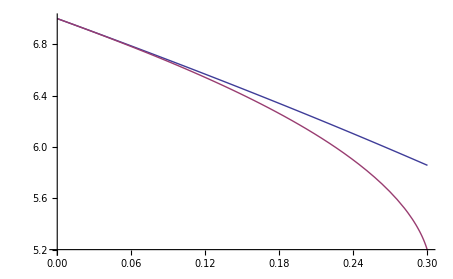

```mathematica
Plot[{feff[7,p],feffx[50,7,p,0]},{p,0,0.3}]
```

```mathematica
(feff[7,.2]-feffx[50,7,.2,0])/feffx[50,7,.2,0]
```

0.0178224

#### Conversion from current to photon number inside the resonator

Here we want to convert current inside the resonator to a photon number. For that we convert one photon to current using linea-resonator electrical and magnetic energy expressions :

```mathematica
Vrms[ωo_,zo_]:=Sqrt[2*hbar*ωo/(Pi / zo / ωo)];
Irms[ωo_,zo_]:=Vrms[ωo,zo]/zo;
ncritiquejct[ωo_,zo_,p_]:=(Ic2[zo,ωo,p]/Irms[ωo,zo])^2;
```

```mathematica
ncritiquejct[2π 7 giga,50,.2]
```

208.017

## Bifurcation points Study

A partir des expressions de β bifurcation de la thèse de metcalfe on trace les courbes de bifurcation

### Mapping utilisé par Metcalfe

Ω is the reduced detuning defined as : Ω = 2 Q δω/ω0
β is the adimensional drive Vb=Sqrt(β) ϕ0bar ω (2 Ω / (p Q))^1.5 (cf M. Metcalfe thesis p. 62)
B is the adimensional charge modulation in the cavity
Details in Agustin's notebook

```mathematica
fromΩtof[Ω_, fo_, p_, Q_] :=feff[fo,p] (1-Ω/2/Q);
fromftoΩ[f_, fo_, p_, Q_] :=2Q(feff[fo,p]-f)/feff[fo,p];
fromβtoVd[Ω_, fo_, p_, Q_, β_] := (2Ω/(p Q))^(1.5)*2*Pi*fromΩtof[Ω, fo, p, Q]*ϕ0b*Sqrt[β];
fromVdtoβ[f_, fo_, p_, Q_, Vd_] := Vd^2 (p Q / 2 / fromftoΩ[f,fo,p,Q])^3 /ϕ0b /(2 π feff[fo,p]);
fromBtoImax[f_,fo_,p_,zo_,B_]:=4  Sqrt[Abs[f-feff[fo,p]]/f/p]  Ic2[zo,2π fo,p]  B;
```

### Definition of the critical point

The critical point is defined by Ωc=\Sqrt[3] and βc=8/27

```mathematica
Ωc=Sqrt[3];
βc=8/27;
Bc=Sqrt[2/3];
fbc[fo_,p_,Q_]:=fromΩtof[Ωc, fo, p, Q];
Vbc[fo_,p_,Q_]:= fromβtoVd[Ωc, fo, p, Q, βc]  ;
Imaxc[fo_,p_,Q_,zo_]:= fromBtoImax[fromΩtof[Ωc, fo, p, Q],fo,p,zo,Bc]  ;
```

### Bifurcation branches in β units

Bifurcation branches βb + - are given following expressions in M.M thesis (p.51) in reduced units of Omega

```mathematica
βbplus[Ω_]:=2/27/Ω^3*(Ω^3+9Ω+(-3+Ω^2)^(3/2))/;Ω>Ωc
βbmoins[Ω_]:=2/27/Ω^3*(Ω^3+9Ω-(-3+Ω^2)^(3/2))/;Ω>Ωc
βbplusf[f_,fo_,p_,Q_]:=βbplus[fromftoΩ[f, fo, p, Q]]/;f<fbc[fo,p,Q]
βbmoinsf[f_,fo_,p_,Q_]:=βbmoins[fromftoΩ[f, fo, p, Q]]/;f<fbc[fo,p,Q]
```

Plots of bifurcation branches

```mathematica
Export[NotebookDirectory[]<>"/jba_beta_vs_omega.csv",Map[Block[{Ω=#},{Ω,1.βbmoins[Ω*Ωc]/βc,1. βbplus[Ω*Ωc]/βc}]&,Range[1.01,5,0.001]]];
```

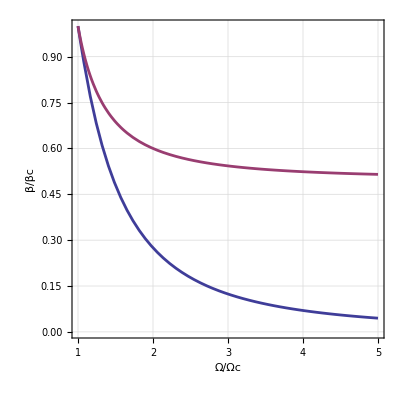

```mathematica
plotβbfctΩ=Plot[{βbmoins[Ω*Ωc]/βc,βbplus[Ω*Ωc]/βc},{Ω,1,5},Evaluate[MyOptions],FrameLabel->{"Ω/Ωc","β/βc","βplus, βmoins",""},Frame->True]
```

```mathematica
criticalvalues = Map[Block[{Ω=#},{Ω,βbmoins[Ω*Ωc]/βc,βbplus[Ω*Ωc]/βc}]&,Range[1.01,5,0.01]];
```

```mathematica
Export[NotebookDirectory[]<>"jba_critical_beta.csv",criticalvalues]
```

E:\cygwin\home\adewes\thesis\material\mathematica\jba_critical_beta.csv

```mathematica
plotβbfctΩ=Plot[{βbmoins[Ω*Ωc]/βc,βbplus[Ω*Ωc]/βc},{Ω,1,5},Evaluate[MyOptions],FrameLabel->{"Ω/Ωc","β/βc","βplus, βmoins",""},Frame->True];
tabβpred=Table[{βred,Ωp/.Last[Solve[2/27*(1+9*1/(Ωp*Ωc)^2+(-3/(Ωp*Ωc)^2+1)^(3/2))/βc==βred,Ωp]]},{βred,.50001,1,.01}];
tabβmred=Table[{βred,Ωp/.Last[Solve[2/27*(1+9*1/(Ωp*Ωc)^2-(-3/(Ωp*Ωc)^2+1)^(3/2))/βc==βred,Ωp]]},{βred,.0001,1,.01}];
plotΩbfctβ=ListPlot[{tabβmred,tabβpred},Joined->True,Evaluate[MyOptions],FrameLabel->{"β/βc","Ω/Ωc","βplus, βmoins",""}];
```

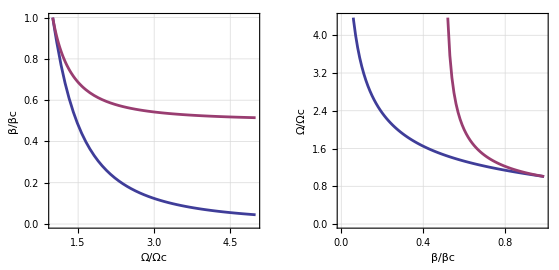

```mathematica
GraphicsRow[{plotβbfctΩ,plotΩbfctβ}]
```

### Bifurcation branches in V units

Bifurcation branches expressed in non - reduced drive units

```mathematica
VdbplusΩ[Ω_/;Ω>Ωc,fo_,p_,Q_]:=fromβtoVd[Ω,fo, p, Q, βbplus[Ω]];
VdbmoinsΩ[Ω_/;Ω>Ωc,fo_,p_,Q_]:=fromβtoVd[Ω,fo, p, Q, βbmoins[Ω]];
Vdbplusf[f_,fo_,p_,Q_]:=fromβtoVd[fromftoΩ[f, fo, p, Q],fo, p, Q, βbplus[fromftoΩ[f, fo, p, Q]]];
Vdbmoinsf[f_,fo_,p_,Q_]:=fromβtoVd[fromftoΩ[f, fo, p, Q],fo, p, Q, βbmoins[fromftoΩ[f, fo, p, Q]]];
```

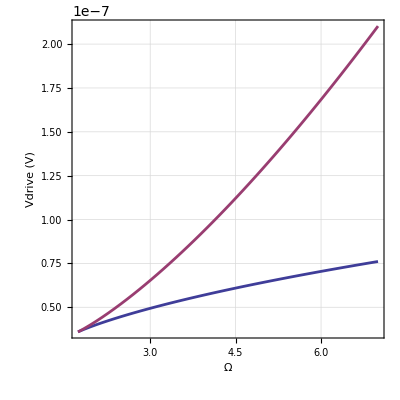

```mathematica
Plot[{VdbmoinsΩ[Ω,7 giga,.23,500],VdbplusΩ[Ω,7 giga,.23,500]},{Ω,Ωc,7},Evaluate[MyOptions],FrameLabel->{"Ω","Vdrive (V)","Vdbplus, Vdbmoins",""}]
```

### Bifurcation branches in B units

Tables with values of B for each branch from Ω = 1 to 10

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

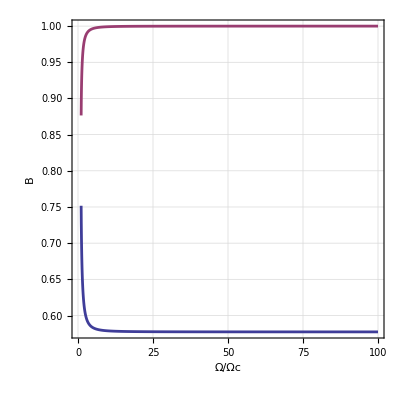

```mathematica
tabB5p=Table[{Ω,Abs[Bp/.Sort[NSolve[Bp^2*(1/(Ω*Ωc)^2+(1-Bp^2)^2)==βbplus[Ω*Ωc],Bp]][[5]]]},{Ω,1,100,.05}];
tabB5m=Table[{Ω,Abs[Bm/.Sort[NSolve[Bm^2*(1/(Ω*Ωc)^2+(1-Bm^2)^2)==βbmoins[Ω*Ωc],Bm]]][[5]]},{Ω,1,100,.05}];
ListPlot[{tabB5p,tabB5m},Evaluate [MyOptions],Joined->True,FrameLabel->{"Ω/Ωc","B","sol avec βb+/-",""}]
```

### Bifurcation branches in Imax/Io units

Critical current units

```mathematica
IcoverIo[fo_,p_,Q_,zo_]:=Imaxc[fo,p,Q,zo]/Ic2[zo,2*Pi*fo,p];
Nptcritique[fo_,p_,Q_,zo_]:=(Imaxc[fo,p,Q,zo]/Irms[2*Pi*fo,zo])^2;
```

```mathematica
Nptcritique[7.33 giga,.217,670,50]
```

10.7689

On peut retrouver le rapport p necessaire pour bifurquer a un certain nombre de photons critique

```mathematica
NSolve[Nptcritique[7.33 giga,p,700,50]==15,p]
```

{}

Plot definitions

```mathematica
PlotImaxc=Plot[Imaxc[7 giga,p,500,50]/micro,{p,0.001,.2},Evaluate[MyOptions],FrameLabel->{"p=Lj/Lt","Ic (µA)","courant du point triple (en µA)",""}];
plotIcocerIo=Plot[IcoverIo[7 giga,p,500,50],{p,0.001,.2},Evaluate[MyOptions],FrameLabel->{"p=Lj/Lt","Ic/Io","courant du point triple (en unité de Io)",""}];
plotNphtoncrit=Plot[Nptcritique[7 giga,p,640,50],{p,0.001,.2},Evaluate[MyOptions],FrameLabel->{"p=Lj/Lt","N photon pt critic","N photon pt critic",""}];
plotNphtoncrit2=Plot[Nptcritique[7 giga,p,640,50],{p,.2,.6},Evaluate[MyOptions],FrameLabel->{"p=Lj/Lt","N photon pt critic","N photon pt critic",""}];
```

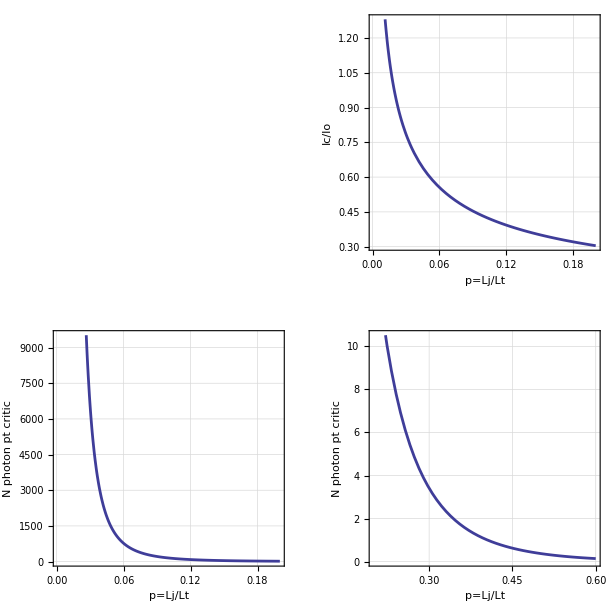

```mathematica
GraphicsGrid[{{PlotIc,plotIcocerIo},{plotNphtoncrit,plotNphtoncrit2}}]
```

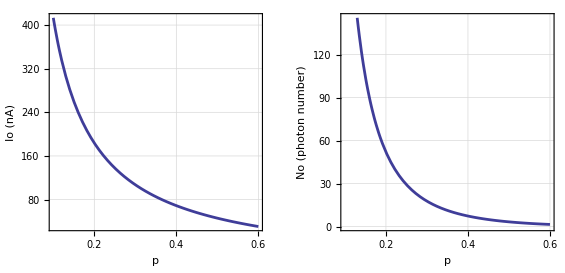

```mathematica
GraphicsRow[{Plot[Ic2[200,2*Pi*7giga,p]/nano,{p,0.1,.6},Evaluate[MyOptions],FrameLabel->{" p ","Io (nA)"," Courant critique de la jonction ", ""}],Plot[ncritiquejct[2*Pi*7giga,200,p],{p,0.1,.6},Evaluate[MyOptions],FrameLabel->{" p ","No (photon number)"," N photon critique jonction", ""}]}]
```

Maintenant on calcule les valeurs des courant de bifurcation, toujours en unité du courant critique

```mathematica
tabIb5p[fo_,p_,Q_]:=Transpose[{Transpose[tabB5p][[1]],fromBtoImax[fromΩtof[Transpose[tabB5p][[1]],fo,p,Q ],fo,p,50,Transpose[tabB5p][[2]]]/Ic2[50,fo 2π,p]}];
tabIb5m[fo_,p_,Q_]:=Transpose[{Transpose[tabB5m][[1]],fromBtoImax[fromΩtof[Transpose[tabB5m][[1]],fo,p,Q ],fo,p,50,Transpose[tabB5m][[2]]]/Ic2[50,fo 2π,p]}];
tabIb5pf[fo_,p_,Q_]:=Transpose[{fromΩtof[Transpose[tabB5p][[1]],fo ,p,Q]/giga,fromBtoImax[fromΩtof[Transpose[tabB5p][[1]],fo,p,Q ],fo,p,50,Transpose[tabB5p][[2]]]/Ic2[50,2π fo,p]}];
tabIb5mf[fo_,p_,Q_]:=Transpose[{fromΩtof[Transpose[tabB5m][[1]],fo ,p,Q]/giga,fromBtoImax[fromΩtof[Transpose[tabB5m][[1]],fo,p,Q ],fo,p,50,Transpose[tabB5m][[2]]]/Ic2[50,2π fo,p]}];
plotIBoverIo[fo_,p_,Q_]:=ListPlot[{tabIb5p[fo ,p,Q],tabIb5m[fo ,p,Q]},Evaluate [MyOptions],Joined->True,FrameLabel->{"Ω/Ωc","Ib/Io","sol avec βb+/-",""}]
plotIBoverIof[fo_,p_,Q_]:=ListPlot[{tabIb5pf[fo ,p,Q],tabIb5mf[fo ,p,Q]},Evaluate [MyOptions],Joined->True,FrameLabel->{"f (GHz)","Ib/Io","sol avec βb+/-",""}]
```

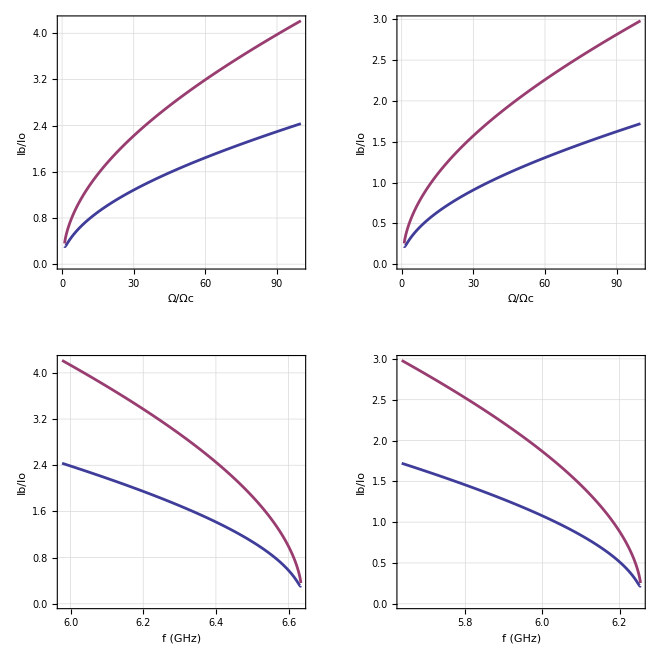

7.3472×10^-7

```mathematica
plot1=Show[plotIBoverIo[7giga,.1,500]];
plot2=Show[plotIBoverIo[7giga,.2,500]];
plot1f=Show[plotIBoverIof[7giga,.1,500]];
plot2f=Show[plotIBoverIof[7giga,.2,500]];
GraphicsGrid[{{plot1,plot2},{plot1f,plot2f}}]
Ic2[50,7giga 2π,0.2]
```

### Bifurcation branches as function of number of photons

```mathematica
tabIbA5p[fo_,p_,Q_,zo_]:=Transpose[{Transpose[tabIb5pf[fo,p,Q]][[1]],1/nano*Ic2[zo,2*Pi*fo ,p]*Transpose[tabIb5pf[fo,p,Q]][[2]]}]
tabIbA5m[fo_,p_,Q_,zo_]:=Transpose[{Transpose[tabIb5mf[fo,p,Q]][[1]],1/nano*Ic2[zo,2*Pi*fo ,p]*Transpose[tabIb5mf[fo,p,Q]][[2]]}]
tabIbN5p[fo_,p_,Q_,zo_]:=Transpose[{Transpose[tabIbA5p[fo,p,Q,zo]][[1]],(nano*Transpose[tabIbA5p[fo,p,Q,zo]][[2]]/Irms[2*Pi*fo,zo])^2}]
tabIbN5m[fo_,p_,Q_,zo_]:=Transpose[{Transpose[tabIbA5m[fo,p,Q,zo]][[1]],(nano*Transpose[tabIbA5m[fo,p,Q,zo]][[2]]/Irms[2*Pi*fo,zo])^2}]
```

```mathematica
tabNcritique[fo_,p_,Q_,zo_]:=Transpose[{Transpose[tabIb5pf[fo,p,Q]][[1]],Transpose[tabIb5pf[fo,p,Q]][[1]]/Transpose[tabIb5pf[fo,p,Q]][[1]]*ncritiquejct[2*Pi*fo giga,zo,p]}];
```

```mathematica
plotNcritique[fo_,p_,Q_]:=Plot[ncritiquejct[2*Pi*fo giga,50,p],{}]
```

```mathematica
t1p[fo_,p_,Q_,zo_]:=Transpose[{Ωc*Transpose[tabB5p][[1]],1/nano*Ic2[100,2*Pi*fo ,p]*Transpose[tabIb5pf[fo,p,Q,zo]][[2]]}]
t1m[fo_,p_,Q_,zo_]:=Transpose[{Ωc*Transpose[tabB5p][[1]],1/nano*Ic2[100,2*Pi*fo ,p]*Transpose[tabIb5mf[fo,p,Q,zo]][[2]]}]
t2p[fo_,p_,Q_,zo_]:=Transpose[{Ωc*Transpose[tabB5p][[1]],(nano*Transpose[tabIbA5p[fo,p,Q,zo]][[2]]/Irms[2*Pi*fo,zo])^2}]
t2m[fo_,p_,Q_,zo_]:=Transpose[{Ωc*Transpose[tabB5p][[1]],(nano*Transpose[tabIbA5m[fo,p,Q,zo]][[2]]/Irms[2*Pi*fo,zo])^2}]
```

```mathematica
plotIB[fo_,p_,Q_,zo_]:=ListPlot[{tabIbA5p[fo ,p,Q,zo],tabIbA5m[fo ,p,Q,zo]},Evaluate [MyOptions],Joined->True,FrameLabel->{"f (GHz)","Ib (nA)","sol avec βb+/-",""}]
plotIN[fo_,p_,Q_,zo_]:=ListPlot[{tabIbN5p[fo ,p,Q,zo],tabIbN5m[fo ,p,Q,zo],tabNcritique[fo ,p,Q,zo]},Evaluate [MyOptions],Joined->True,FrameLabel->{"f (GHz)","Nbre de photons","sol avec βb+/-",""}]
```

```mathematica
plotINΩ[fo_,p_,Q_,zo_]:=ListPlot[{t2p[fo ,p,Q,zo],t2m[fo ,p,Q,zo]},PlotRange->{{1,10},{0,100}},Evaluate[MyOptions]]
```

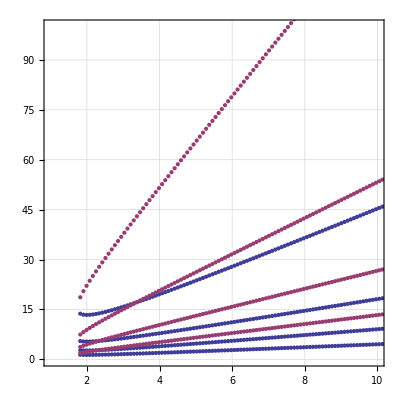

```mathematica
Show[{plotINΩ[7 giga,0.2,900,20],plotINΩ[7 giga,0.2,900,50],plotINΩ[7 giga,0.2,900,100],plotINΩ[7 giga,0.2,900,200]}]
```

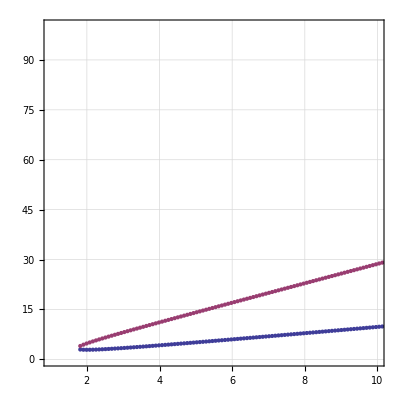

```mathematica
plotINΩ[7 giga,0.16,900,200]
```

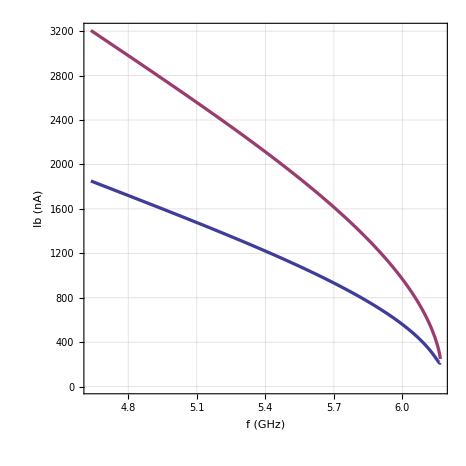

```mathematica
plotIB[7 giga,.22,200,50]
```

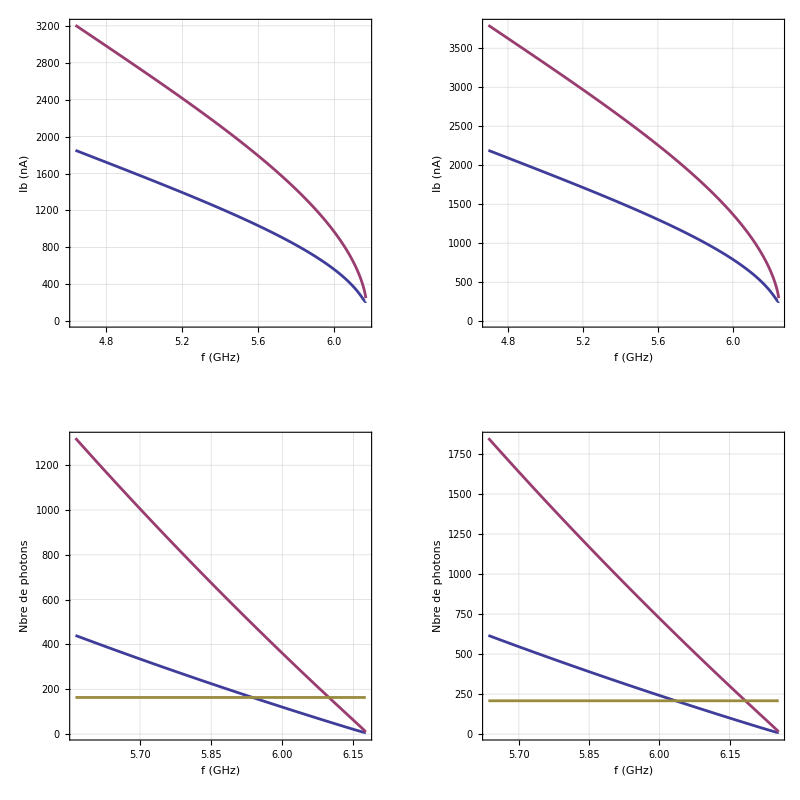

```mathematica
plot1B=Show[plotIB[7 giga,.22,200,50]];
plot2B=Show[plotIB[7 giga,.2,200,50]];
plot1N=plotIN[7 giga,.22,500,50];
plot2N=plotIN[7 giga,.2,500,50];
GraphicsGrid[{{plot1B,plot2B},{plot1N,plot2N}}]
```

## Stationnary Regime

### Mapping F Mallet

(L + Lj) q'' + Rq' + q/C + Lj/2 io^2 q'^2 q'' = v cos(wt)
	équivalent à  
(ωo^2 - ω^2) A + 2 iωA' + 2 ΓiωA - p/(8 Io^2) ω^4 | A | ^2 A = v/Lt pas de 2
	en posant Lt = L + Lj, ω0^2 = 1/LtC, 2 Γ = R/Lt, q (t) = 2 Re[A (t) expiωt], p = Lj/Lt
	équivalent à
B ((1 - f^2 - f^4 B/8) + 4 γ^2 f^2) = α^2
	en posant f = ω/ω0, γ = Γ/ω0, cA = Io/(Sqrt[p]*ω0)*Sqrt[B], α =  v p^(1.5)/(ϕ0 ω0) pas de 2

```mathematica
fromΩtofred[Ω_,fo_,p_,Q_]:=fromΩtof[Ω, fo, p, Q]/fo;
fromQtoγ[Q_]:=1/2/Q;
fromVdtoα[fo_,p_,v_]:=v*p^(1.5)/ϕ0b/(2π fo);
fromBMtoI[f_,fo_,p_,B_]:=B  Ic2[50,2 π fo, p] f/fo /Sqrt[p];
```

### Stationnary Solutions

Equation Cubique en B=A^2 (A amplitude de la phase de la jonction),

```mathematica
sol0=Map[#[[1,2]]&,Solve[{B*((1-f^2-f^4*B/8)^2+4*γ^2 f^2)==α^2},B]];
```

Amplitude de la phase : Résolution de l'équation (3 solutions), seules les solutions réelles sont physiques car on s'intéresse à l'amplitude de la phase de la jonction
Amp donne toujours une liste de 3 solutions, les solutions non physiques sont remplacées par I. amp1, amp2 et amp3 donnent une des 3 solutions séparement

```mathematica
amp[f_,α_,γ_] =Sqrt[Map[If[Abs[Im[#]]<10^(-6),Re[#],I]&,sol0]];
amp1[f_,α_,γ_]:=amp[f,α,γ][[1]];
amp2[f_,α_,γ_]:=amp[f,α,γ][[2]];
amp3[f_,α_,γ_]:=amp[f,α,γ][[3]];
```

Phase du mouvement : Résolution de l'équation (3 solutions), seules les soluitions réelles sont physiques.
Phase  donne toujours une liste de 3 solutions, les solutions non physiques sont remplacées par I. phase1, phase2 et phase3 donnent une des 3 solutions séparement

```mathematica
phase[f_,α_,γ_]:=Map[If[Im[#]≠0,I,ArcTan[f^2-1+f^4*#^2/8,2*f*γ]]&,amp[f,α,γ]];
phase1[f_,α_,γ_]:=phase[f,α,γ][[1]];
phase2[f_,α_,γ_]:=phase[f,α,γ][[2]];
phase3[f_,α_,γ_]:=phase[f,α,γ][[3]];
```

Analytical solution of 3rd degree equation

a3d := -2;
b3d[Ω_] := 1 + 1/Ω^2;
c3d[β_] := -β;
p3d[Ω_] := b3d[Ω] - a3d^2/3;
q3d[Ω_, β_] := c3d[β] + (2*a3d^3 - 9*a3d*b3d[Ω])/27;
u3d[Ω_, β_] := Power[-q3d[Ω, β]/2 + Sqrt[q3d[Ω, β]^2/4 + p3d[Ω]^3/27], 1/3];
u3d2[Ω_, β_] := Power[-q3d[Ω, β]/2 - Sqrt[q3d[Ω, β]^2/4 + p3d[Ω]^3/27], 1/3];
sol3d[Ω_, β_] := -p3d[Ω]/3/u3d[Ω, β] + u3d[Ω, β] - a3d/3;
sol3d2[Ω_, β_] := -p3d[Ω]/3/u3d2[Ω, β] + u3d2[Ω, β] - a3d/3;

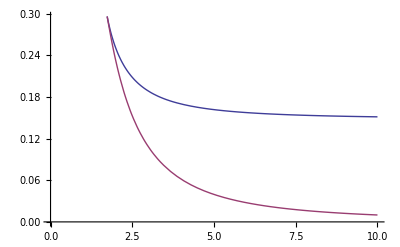

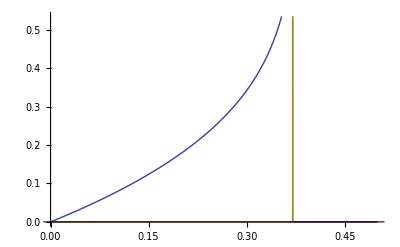

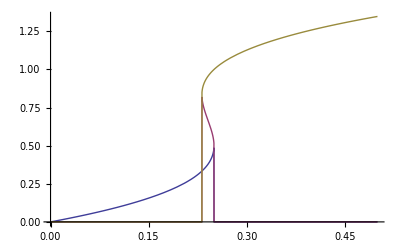

{0.123806,0.669192,1.207}

```mathematica
Plot[{βbplus[Ω],βbmoins[Ω]},{Ω,0,10}]
solss[Ω_,β_]:=Map[If[Im[#]≠0,I,#]&,Map[#[[1,2]]&,Solve[u2/Ω^2+u2*(u2-1)^2==β,u2]]];
amp1[Ω_,β_]:=Re[solss[Ω,β][[1]]];
amp2[Ω_,β_]:=Re[solss[Ω,β][[2]]];
amp3[Ω_,β_]:=Re[solss[Ω,β][[3]]];

Plot[{amp1[1.5,β],amp2[1.5,β],amp3[1.5,β]},{β,0,0.5}]
Plot[{amp1[2,β],amp2[2,β],amp3[2,β]},{β,0,0.5}]





solss[5,.1]
```

```mathematica
Plot[{amp1[f,α,fromQtoγ[685]],amp2[f,α,fromQtoγ[685]],amp3[f,α,fromQtoγ[685]]}]
```

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

Plot[{amp1[f,α,fromQtoγ[685]],amp2[f,α,fromQtoγ[685]],amp3[f,α,fromQtoγ[685]]}]

Plot::argrx: Plot called with 0 arguments; 2 arguments are expected.

Plot[]

### Amplitude de l'oscillation Sqrt[B] en fct de α, γ

```mathematica
$DisplayFunction
```

Identity

```mathematica
plotamp[α_,γ_,opts___]:=Plot[{amp1[f,α,γ],amp2[f,α,γ],amp3[f,α,γ]},{f,0.5,1.5},PlotStyle->{RGBColor[1,0,0],RGBColor[0,1,0],RGBColor[0,0,1]},Frame->True,PlotRange->Full,Axes->False,opts,Evaluate[MyOptions]]
```

```mathematica
Show[Table[{amp1[f,α,γ],amp2[f,α,γ],amp3[f,α,γ]} [α,10^-2,DisplayFunction->Identity],{α,0.01,0.12,0.01}],PlotRange->Full]
```

```mathematica
plot1=Show[Table[plotamp[α,10^-3,DisplayFunction->Identity],{α,0.01,0.12,0.01}],DisplayFunction->$DisplayFunction,PlotRange->All,FrameLabel->{"ω/ω0 ","Sqrt[B]~A","q(t)=Aexpiωt vs ω/ω0 for {α,0.01,0.12,0.01},γ=10^-3",""},Frame->True];
```

```mathematica
plot2=Show[Table[plotamp[α,10^-2,DisplayFunction->Identity],{α,0.05,0.05,0.01}],DisplayFunction->$DisplayFunction,PlotRange->All,FrameLabel->{"ω/ω0 ","Sqrt[B]~A","",""},Frame->True];
```

```mathematica
plot3=Show[Table[plotamp[α,3*10^-2,DisplayFunction->Identity],{α,0.01,0.12,0.01}],DisplayFunction->$DisplayFunction,PlotRange->All,FrameLabel->{"ω/ω0 ","Sqrt[B]~A","q(t)=Aexpiωt vs reduced detuning for {α,0.01,0.12,0.01},γ=3.10^-2",""},Frame->True];
```

```mathematica
plot4=Show[Table[plotamp[α,5*10^-2,DisplayFunction->Identity],{α,0.01,0.12,0.01}],DisplayFunction->$DisplayFunction,PlotRange->All,FrameLabel->{"ω/ω0 ","Sqrt[B]~A","q(t)=Aexpiωt vs ω/ω0 for {α,0.01,0.12,0.01},γ=5.10^-2",""},Frame->True];
```

```mathematica
Element[4., Reals]
```

True

```mathematica
values1 = Select[Map[Block[{f=#},{f,1.phase1[f,α,γ]} /. {α->0.05,γ->10^-2}]&,Range[0.5,1.5,0.0025]],Element[#[[2]],Reals]&] ;
values2 = Select[Map[Block[{f=#},{f,1.phase2[f,α,γ]} /. {α->0.05,γ->10^-2}]&,Range[0.5,1.5,0.0025]],Element[#[[2]],Reals]&] ;
values3 = Select[Map[Block[{f=#},{f,1.phase3[f,α,γ]} /. {α->0.05,γ->10^-2}]&,Range[0.5,1.5,0.0025]],Element[#[[2]],Reals] &];
```

```mathematica
Export[NotebookDirectory[]<>"jba_phase_alpha=0p05_gamma=0p01_1.csv",values1]
Export[NotebookDirectory[]<>"jba_phase_alpha=0p05_gamma=0p01_2.csv",values2]
Export[NotebookDirectory[]<>"jba_phase_alpha=0p05_gamma=0p01_3.csv",values3]
```

E:\cygwin\home\adewes\thesis\material\mathematica\jba_phase_alpha=0p05_gamma=0p01_1.csv

E:\cygwin\home\adewes\thesis\material\mathematica\jba_phase_alpha=0p05_gamma=0p01_2.csv

E:\cygwin\home\adewes\thesis\material\mathematica\jba_phase_alpha=0p05_gamma=0p01_3.csv

```mathematica
values3
```

{{0.75,1.65686},{0.7525,1.72953},{0.755,1.77606},{0.7575,1.81325},{0.76,1.84518},{0.7625,1.87362},{0.765,1.89952},{0.7675,1.92347},{0.77,1.94588},{0.7725,1.967},{0.775,1.98705},{0.7775,2.00619},{0.78,2.02453},{0.7825,2.04217},{0.785,2.0592},{0.7875,2.07568},{0.79,2.09166},{0.7925,2.1072},{0.795,2.12234},{0.7975,2.1371},{0.8,2.15153},{0.8025,2.16564},{0.805,2.17947},{0.8075,2.19303},{0.81,2.20635},{0.8125,2.21945},{0.815,2.23233},{0.8175,2.24502},{0.82,2.25752},{0.8225,2.26986},{0.825,2.28204},{0.8275,2.29407},{0.83,2.30597},{0.8325,2.31774},{0.835,2.32939},{0.8375,2.34094},{0.84,2.35238},{0.8425,2.36373},{0.845,2.375},{0.8475,2.38619},{0.85,2.39732},{0.8525,2.40838},{0.855,2.41938},{0.8575,2.43034},{0.86,2.44126},{0.8625,2.45214},{0.865,2.46299},{0.8675,2.47383},{0.87,2.48465},{0.8725,2.49547},{0.875,2.50628},{0.8775,2.51711},{0.88,2.52796},{0.8825,2.53884},{0.885,2.54976},{0.8875,2.56072},{0.89,2.57174},{0.8925,2.58284},{0.895,2.59402},{0.8975,2.6053},{0.9,2.61669},{0.9025,2.62823},{0.905,2.63992},{0.9075,2.65179},{0.91,2.66388},{0.9125,2.67622},{0.915,2.68886},{0.9175,2.70184},{0.92,2.71524},{0.9225,2.72915},{0.925,2.7437},{0.9275,2.75906},{0.93,2.77551},{0.9325,2.79348},{0.935,2.81384},{0.9375,2.83868},{0.94,2.87987}}

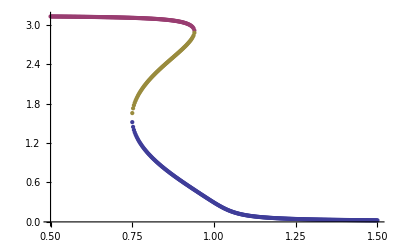

```mathematica
ListPlot[{values1,values2,values3}]
```

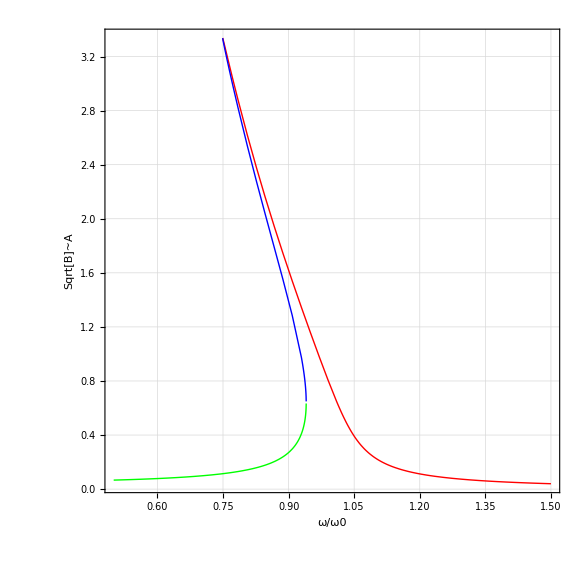

```mathematica
plot2
```

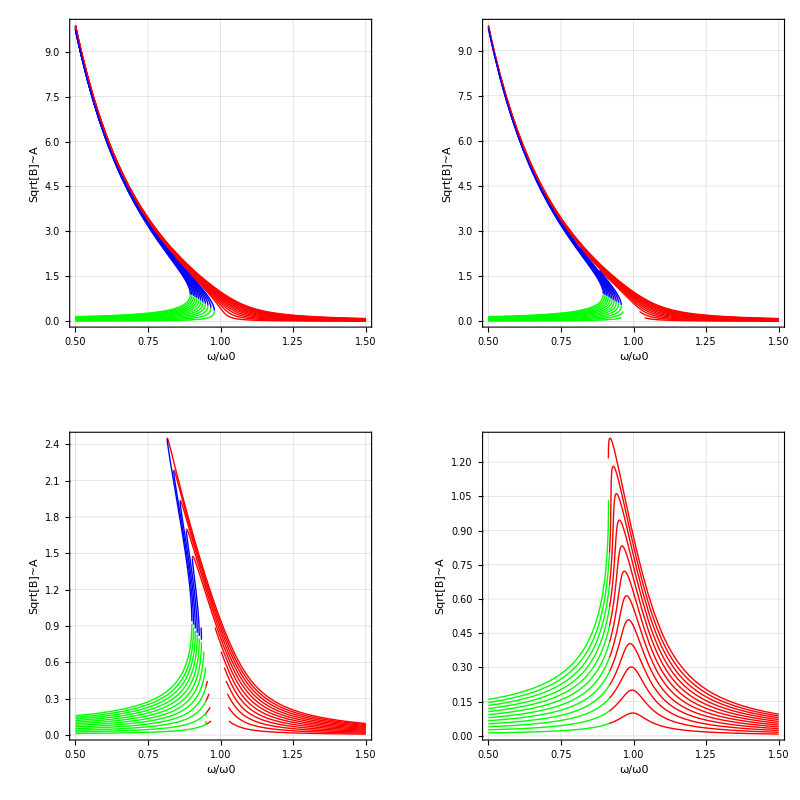

```mathematica
GraphicsGrid[{{plot1,plot2},{plot3,plot4}}]
```

### Amplitude du courant I en fct de vd, Q, ω, p

```mathematica
para1={ω0->2*Pi*7.33giga};
para2={f0->7.33giga};
```

```mathematica
Aampl1[f_,p_,v_,Q_]:= fromBMtoI[f,feff[f0,p],p,amp1[f/feff[f0,p],fromVdtoα[f0,p,v],fromQtoγ[Q]]/.para2] ;
Aampl2[f_,p_,v_,Q_]:= fromBMtoI[f,feff[f0,p],p,amp2[f/feff[f0,p],fromVdtoα[f0,p,v],fromQtoγ[Q]]/.para2] ;
Aampl3[f_,p_,v_,Q_]:= fromBMtoI[f,feff[f0,p],p,amp3[f/feff[f0,p],fromVdtoα[f0,p,v],fromQtoγ[Q]]/.para2];
```

```mathematica
Aampl1[7giga,.2,.01,500]
```

0.0000116694

```mathematica
plotAAamp[p_,v_,Q_]:=Plot[{Aampl1[f giga,p,v,Q]/micro,Aampl2[f giga,p,v,Q]/micro,Aampl3[f giga,p,v,Q]/micro},{f,6,7},PlotStyle->{RGBColor[1,0,0],RGBColor[0,1,0],RGBColor[0,0,1]},Frame->True,Axes->False,Evaluate[MyOptions],PlotRange->All]
```

```mathematica
plotBAamp1=Show[Table[plotAAamp[0.224,v,700]/.para1,{v,10^(-9),10^(-7),0.5 10^(-8)}],FrameLabel->{" f(GHz) ","I (µA)"," {v,e-9,e-7,0.5e-8},Q=700, p=0.224", ""},Frame->True];
```

Power::infy: Infinite expression 1/0.^1/3 encountered.

```mathematica
plotBAamp2=Show[Table[plotAAamp[0.13,v,500]/.para1,{v,10^-8,10^-6,10^-7}],FrameLabel->{" f(GHz) ","I (µA)"," {v,e-8,e-6,e-7},Q=500, p=0.13", ""},Frame->True];
```

Power::infy: Infinite expression 1/0.^1/3 encountered.

```mathematica
plotBAamp3=Show[Table[plotAAamp[0.16,v,500]/.para1,{v,10^-8,10^-6,10^-7}],FrameLabel->{" f(GHz) ","I (µA)"," {v,e-8,e-6,e-7},Q=500, p=0.16", ""},Frame->True];
```

```mathematica
plotBAamp4=Show[Table[plotAAamp[0.2,v,500]/.para1,{v,10^-8,10^-6,10^-7}],FrameLabel->{" f(GHz) ","I (µA)"," {v,e-8,e-6,e-7},Q=500, p=0.2", ""},Frame->True];
```

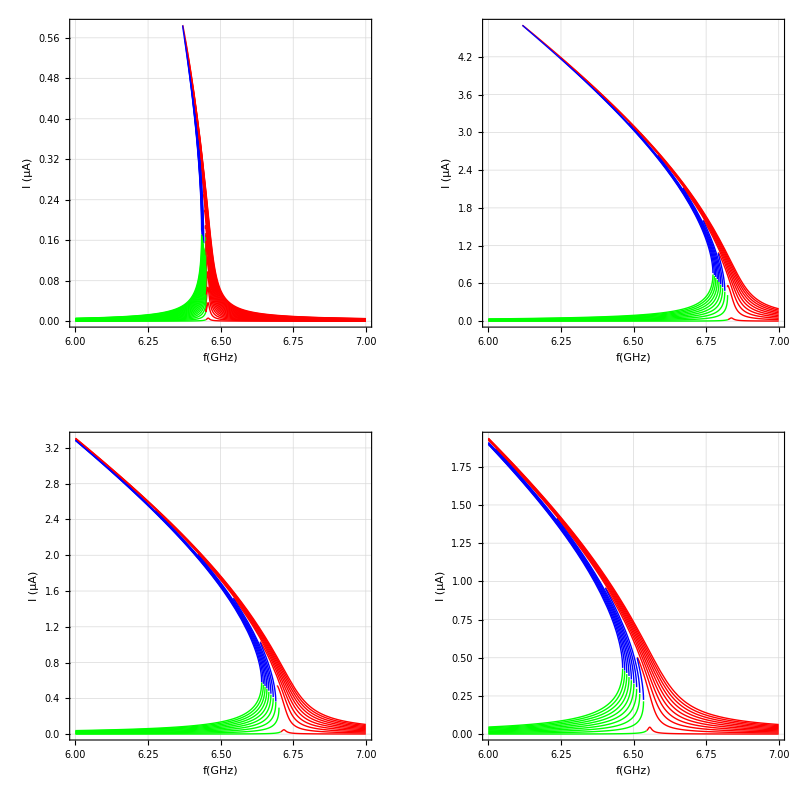

```mathematica
GraphicsGrid[{{plotBAamp1,plotBAamp2},{plotBAamp3,plotBAamp4}},PlotRange->{{5.6giga,6giga},{0,1}}]
```

### Number of photons (en fct de vd, Q, ω, p)

```mathematica
Nampl1[f_,p_,v_,Q_]:=(Aampl1[f,p,v,Q]/Irms[2*Pi*f,50])^2;
Nampl2[f_,p_,v_,Q_]:=(Aampl2[f,p,v,Q]/Irms[2*Pi*f,50])^2;
Nampl3[f_,p_,v_,Q_]:=(Aampl3[f,p,v,Q]/Irms[2*Pi*f,50])^2;
```

```mathematica
plotNAamp[p_,v_,Q_]:=Plot[{Nampl1[f giga,p,v,Q],Nampl2[f giga,p,v,Q],Nampl3[f giga,p,v,Q],ncritiquejct[2*Pi*7 giga,50,p],20,Nptcritique[7 giga,p,Q]},{f,5,7},PlotStyle->{RGBColor[1,0,0],RGBColor[0,1,0],RGBColor[0,0,1],RGBColor[1,0,0],RGBColor[0,1,0],RGBColor[0,0,1]},Frame->True,Axes->False,Evaluate[MyOptions],PlotRange->All]
```

```mathematica
plotNAamp11=Show[{plotIN[7.33giga,.1,500,50],Table[plotNAamp[0.1,v,500]/.para1,{v,10^-8,5*10^-7,5*10^-8}]},FrameLabel->{" f(GHz) ","I (photon)"," {v,e-8,e-6,e-7},Q=500, p=0.1", ""},Frame->True,PlotRange-> {{6.8,7},{0,400}}];
```

Power::infy: Infinite expression 1/0.^1/3 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

```mathematica
plotNAamp12=Show[{plotIN[7.33giga,.13,500,50],Table[plotNAamp[0.13,v,500]/.para1,{v,10^-8,10^-6,10^-7}]},FrameLabel->{" f(GHz) ","I (photon)"," {v,e-8,e-6,e-7},Q=500, p=0.13", ""},Frame->True,PlotRange-> {{6.5,6.9},{0,400}}];
```

Power::infy: Infinite expression 1/0.^1/3 encountered.

```mathematica
plotNAamp13=Show[{plotIN[7.33giga,.16,500,50],Table[plotNAamp[0.16,v,500]/.para1,{v,10^-8,10^-6,10^-7}]},FrameLabel->{" f(GHz) ","I (photon)"," {v,e-8,e-6,e-7},Q=500, p=0.16", ""},Frame->True,PlotRange-> {{6.6,6.8},{0,400}}];
```

Power::infy: Infinite expression 1/0.^1/3 encountered.

```mathematica
plotNAamp14=Show[{plotIN[7.33giga,.2,500,50],Table[plotNAamp[0.2,v,500]/.para1,{v,10^-8,10^-6,10^-7}]},FrameLabel->{" f(GHz) ","I (photon)"," {v,e-8,e-6,e-7},Q=500, p=0.2", ""},Frame->True,PlotRange-> {{6.4,6.6},{0,400}}];
```

Power::infy: Infinite expression 1/0.^1/3 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

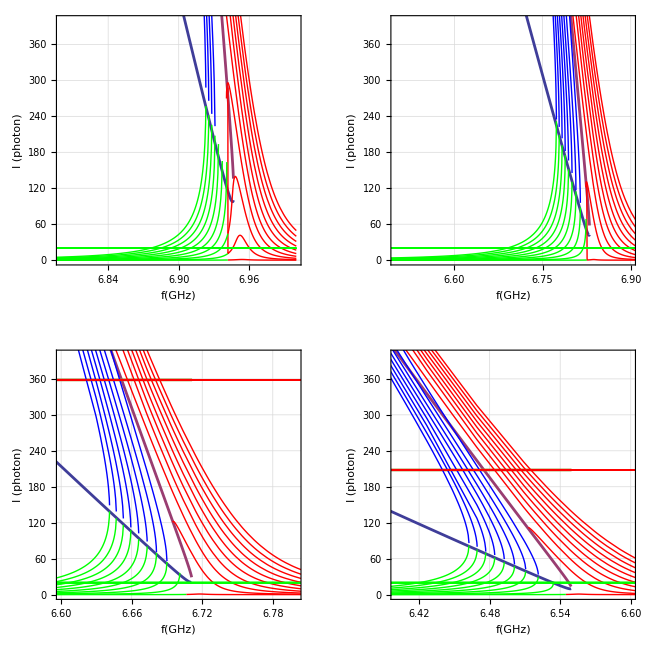

```mathematica
GraphicsGrid[{{plotNAamp11,plotNAamp12},{plotNAamp13,plotNAamp14}}]
```

```mathematica
plotNAamp1=Show[{plotIN[7 giga,.23,500,50],Table[plotNAamp[0.23,v,500]/.para1,{v,10^-8,10^-7,10^-8}]},PlotRange->{{5.9,6.1},{0,200}},FrameLabel->{" f(GHz) ","I (photon)"," {v,e-8,e-6,e-7},Q=500, p=0.23", ""},Frame->True];
```

Power::infy: Infinite expression 1/0.^1/3 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

```mathematica
plotNAamp2=Show[{plotIN[7 giga,.26,500,50],Table[plotNAamp[0.26,v,500]/.para1,{v,10^-8,10^-7,10^-8}]},PlotRange->{{5.8,6},{0,200}},FrameLabel->{" f(GHz) ","I (photon)"," {v,e-8,e-6,e-7},Q=500, p=0.26", ""},Frame->True];
```

Power::infy: Infinite expression 1/0.^1/3 encountered.

```mathematica
plotNAamp3=Show[{plotIN[7 giga,.29,500,50],Table[plotNAamp[0.29,v,500]/.para1,{v,10^-8,10^-7,10^-8}]},PlotRange->{{5.65,5.85},{0,200}},FrameLabel->{" f(GHz) ","I (photon)"," {v,e-8,e-6,e-7},Q=500, p=0.29", ""},Frame->True];
```

Power::infy: Infinite expression 1/0.^1/3 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

```mathematica
plotNAamp4=Show[{plotIN[7 giga,.32,500,50],Table[plotNAamp[0.32,v,500]/.para1,{v,10^-8,10^-7,10^-8}]},PlotRange->{{5.5,5.7},{0,200}},FrameLabel->{" f(GHz) ","I (photon)"," {v,e-8,e-6,e-7},Q=500, p=0.32", ""},Frame->True];
```

Power::infy: Infinite expression 1/0.^1/3 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

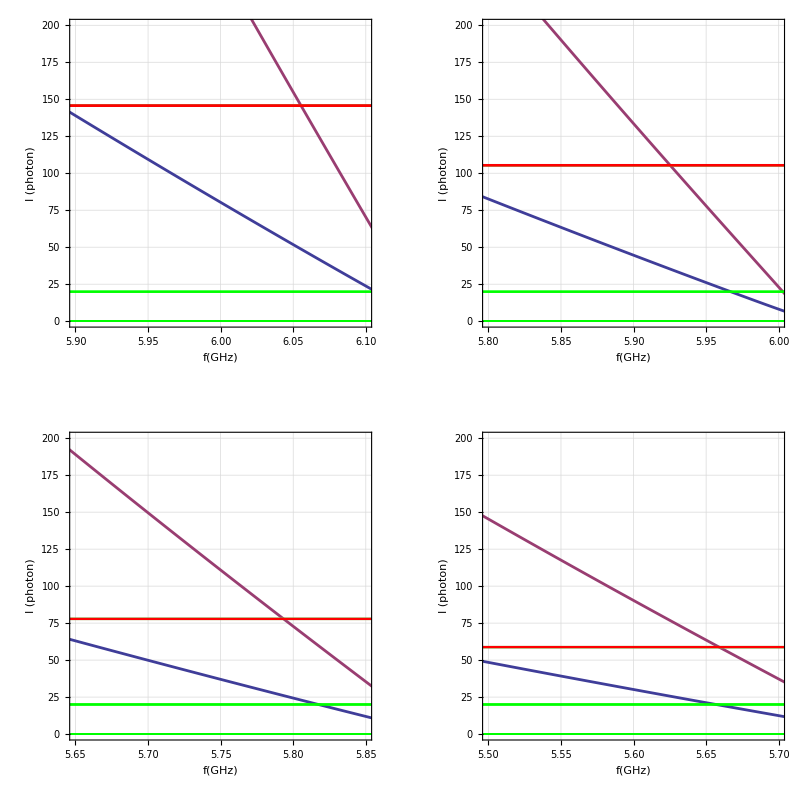

```mathematica
GraphicsGrid[{{plotNAamp1,plotNAamp2},{plotNAamp3,plotNAamp4}}]
```

### Amplitude du courant I/Io en fct de vd, Q, ω, p (Io courant critique de la jonction)

```mathematica
para1={ω0->2*Pi*7 giga};
```

```mathematica
Bampl1[f_,p_,v_,Q_]:=Block[{γ=1/(2Q),α=2*v*p^(1.5)/(φ0*ωeff[ω0,p])},(2*Pi*f)/(p^.5*ωeff[ω0,p])*amp1[2*Pi*f/ωeff[ω0,p],α,γ]]/.para1
Bampl2[f_,p_,v_,Q_]:=Block[{γ=1/(2Q),α=2*v*p^(1.5)/(φ0*ωeff[ω0,p])},(2*Pi*f)/(p^.5*ωeff[ω0,p])*amp2[2*Pi*f/ωeff[ω0,p],α,γ]]/.para1
Bampl3[f_,p_,v_,Q_]:=Block[{γ=1/(2Q),α=2*v*p^(1.5)/(φ0*ωeff[ω0,p])},(2*Pi*f)/(p^.5*ωeff[ω0,p])*amp3[2*Pi*f/ωeff[ω0,p],α,γ]]/.para1
```

```mathematica
plotABamp[p_,v_,Q_]:=Plot[{Bampl1[f giga,p,v,Q],Bampl2[f giga,p,v,Q],Bampl3[f giga,p,v,Q],IcoverIo[7 giga,p,Q],1,Sqrt[20]*Irms[2*Pi*7 giga,50]/Ic2[50,2*Pi*7 giga,p]},{f,5,7},PlotStyle->{RGBColor[1,0,0],RGBColor[0,1,0],RGBColor[0,0,1]},Frame->True,Axes->False,Evaluate[MyOptions],PlotRange->All]
```

```mathematica
plotCAamp11=Show[{plotIBoverIof[7 ,.1,500],Table[plotABamp[0.1,v,500]/.para1,{v,2*10^-8,4*10^-7,5*10^-8}]},plotIBoverIof[7 giga,.1,500],PlotRange->{{6.3,6.7},{0,1.5}},FrameLabel->{" f(GHz) ","I/Ic"," {v,2e-8,4e-7,5e-8},Q=500, p=0.1", ""},Frame->True];
```

Power::infy: Infinite expression 1/0.^1/3 encountered.

```mathematica
plotCAamp12=Show[{plotIBoverIof[7 ,.13,500],Table[plotABamp[0.13,v,500]/.para1,{v,2*10^-9,2*10^-7,2*10^-8}]},PlotRange->{{6.25,6.55},{0,1.5}},FrameLabel->{" f(GHz) ","I/Ic"," {v,2e-9,2e-7,2e-8},Q=500, p=0.13", ""},Frame->True];
```

Power::infy: Infinite expression 1/0.^1/3 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

```mathematica
plotCAamp13=Show[{plotIBoverIof[7 ,.16,500],Table[plotABamp[0.16,v,500]/.para1,{v,2*10^-9,1.4*10^-7,2*10^-8}]},PlotRange->{{6.15,6.45},{0,1.5}},FrameLabel->{" f(GHz) ","I/Ic"," {v,2e-7,1.4e-7,2e-8},Q=500, p=0.16", ""},Frame->True];
```

Power::infy: Infinite expression 1/0.^1/3 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

```mathematica
plotCAamp14=Show[{plotIBoverIof[7 ,.2,500],Table[plotABamp[0.2,v,500]/.para1,{v,2*10^-9,10^-7,10^-8}]},PlotRange->{{6,6.25},{0,1.5}},FrameLabel->{" f(GHz) ","I/Ic"," {v,2e-9,e-7,2e-8},Q=500, p=0.2", ""},Frame->True];
```

Power::infy: Infinite expression 1/0.^1/3 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

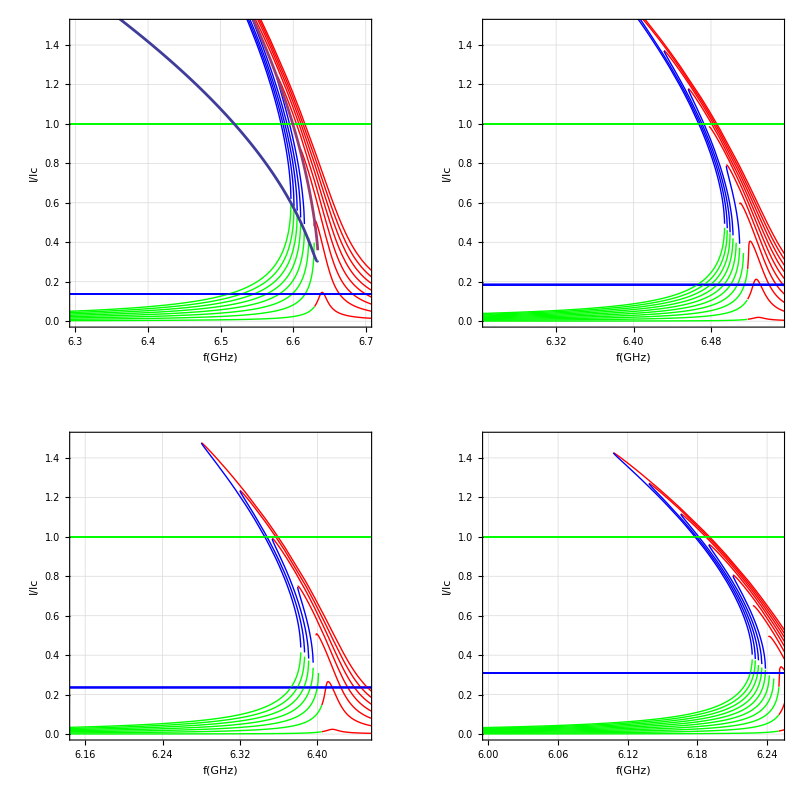

```mathematica
GraphicsGrid[{{plotCAamp11,plotCAamp12},{plotCAamp13,plotCAamp14}}]
```

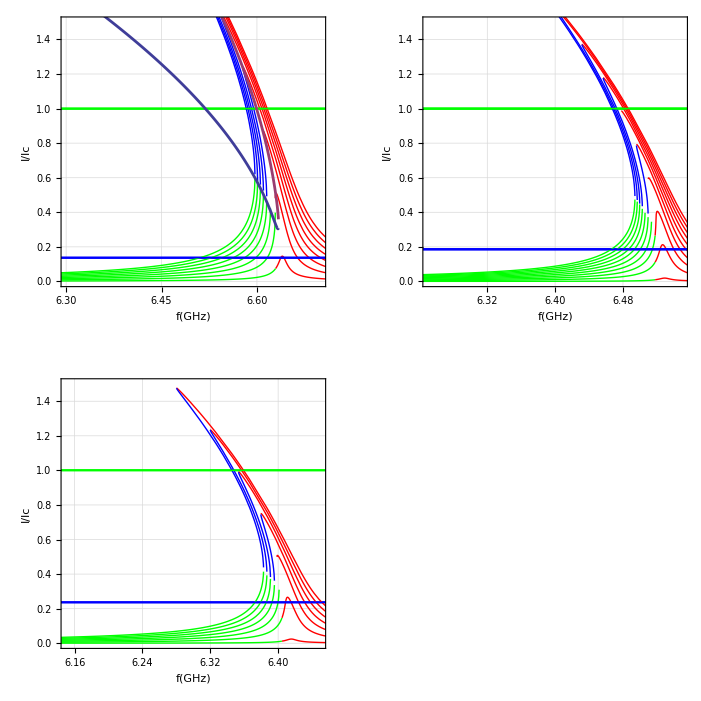

-Graphics-

```mathematica
plotCAamp21=Show[{plotIBoverIof[7 ,.23,500],Table[plotABamp[0.23,v,500]/.para1,{v,2*10^-8,4*10^-7,5*10^-8}]},PlotRange->{{5.8,6.2},{0,1.5}},FrameLabel->{" f(GHz) ","I/Ic"," {v,2e-8,4e-7,5e-8},Q=500, p=0.23", ""},Frame->True];
```

```mathematica
plotCAamp22=Show[{plotIBoverIof[7 ,.26,500],Table[plotABamp[0.26,v,500]/.para1,{v,2*10^-9,1.4*10^-7,2*10^-8}]},PlotRange->{{5.7,6.1},{0,1.5}},FrameLabel->{" f(GHz) ","I/Ic"," {v,2e-9,1.4e-7,2e-8},Q=500, p=0.26", ""},Frame->True];
```

Power::infy: Infinite expression 1/0.^1/3 encountered.

```mathematica
plotCAamp23=Show[{plotIBoverIof[7 ,.29,500],Table[plotABamp[0.29,v,500]/.para1,{v,2*10^-9,1.4*10^-7,2*10^-8}]},PlotRange->{{5.5,5.95},{0,1.5}},FrameLabel->{" f(GHz) ","I/Ic"," {v,2e-7,1.4e-7,2e-8},Q=500, p=0.29", ""},Frame->True];
```

Power::infy: Infinite expression 1/0.^1/3 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

```mathematica
plotCAamp24=Show[{plotIBoverIof[7 ,.32,500],Table[plotABamp[0.32,v,500]/.para1,{v,2*10^-9,10^-7,10^-8}]},PlotRange->{{5.5,5.75},{0,1.5}},FrameLabel->{" f(GHz) ","I/Ic"," {v,2e-9,e-7,2e-8},Q=500, p=0.32", ""},Frame->True];
```

Power::infy: Infinite expression 1/0.^1/3 encountered.

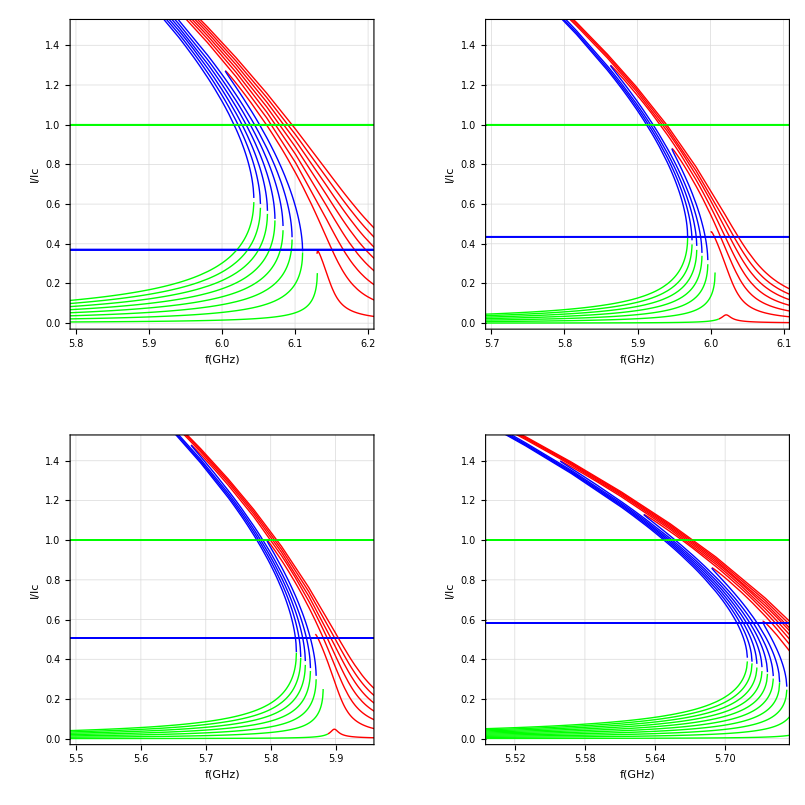

```mathematica
GraphicsGrid[{{plotCAamp21,plotCAamp22},{plotCAamp23,plotCAamp24}}]
```

### Phase de l'oscillation Arg[Sqrt[B]] en fct de α, γCORROMPU!!!!!!!!!!!!

### Phase de l'oscillation Arg[Sqrt[B]] en fct de vd, Q, ω, p

```mathematica
para1={ω0->2*Pi*7giga};
```

```mathematica
Bphase1[f_,p_,v_,Q_]:=Block[{γ=1/(2Q),α=2*v*p^(1.5)/(φ0*ωeff[ω0,p])},phase1[2*Pi*f/ωeff[ω0,p],α,γ]]/.para1
Bphase2[f_,p_,v_,Q_]:=Block[{γ=1/(2Q),α=2*v*p^(1.5)/(φ0*ωeff[ω0,p])}, phase2[2*Pi*f/ωeff[ω0,p],α,γ]]/.para1
Bphase3[f_,p_,v_,Q_]:=Block[{γ=1/(2Q),α=2*v*p^(1.5)/(φ0*ωeff[ω0,p])}, phase3[2*Pi*f/ωeff[ω0,p],α,γ]]/.para1
```

```mathematica
plotBphase[p_,v_,Q_]:=Plot[{Bphase1[f giga,p,v,Q],Bphase2[f giga,p,v,Q],Bphase3[f giga,p,v,Q]},{f,0,10},PlotStyle->{RGBColor[1,0,0],RGBColor[0,1,0],RGBColor[0,0,1]},Frame->True,Axes->False,Evaluate[MyOptions]]
```

```mathematica
0
```

0

```mathematica
plotBphase1=Show[Table[plotBphase[0.1,v,500]/.para1,{v,10^-8,10^-7,10^-8}],PlotRange->{{6.4,6.6},All},FrameLabel->{" f(GHz) ","Arg[Sqrt[B]]~Arg[A]"," {v,e-8,e-7,e-8},Q=500, p=0.1", ""},Frame->True];
```

```mathematica
plotBphase2=Show[Table[plotBphase[0.13,v,500]/.para1,{v,10^-8,10^-7,10^-8}],PlotRange->{{6.3,6.45},All},FrameLabel->{" f(GHz) ","Arg[Sqrt[B]]~Arg[A]"," {v,e-8,e-7,e-8},Q=500, p=0.13", ""},Frame->True];
```

```mathematica
plotBphase3=Show[Table[plotBphase[0.16,v,500]/.para1,{v,10^-8,10^-7,10^-8}],PlotRange->{{6.15,6.35},All},FrameLabel->{" f(GHz) ","Arg[Sqrt[B]]~Arg[A]"," {v,e-8,e-7,e-8},Q=500, p=0.16", ""},Frame->True];
```

```mathematica
plotBphase4=Show[Table[plotBphase[0.19,v,500]/.para1,{v,10^-8,10^-7,10^-8}],PlotRange->{{6.05,6.25},All},FrameLabel->{" f(GHz) ","Arg[Sqrt[B]]~Arg[A]"," {v,e-8,e-7,e-8},Q=500, p=0.19", ""},Frame->True];
```

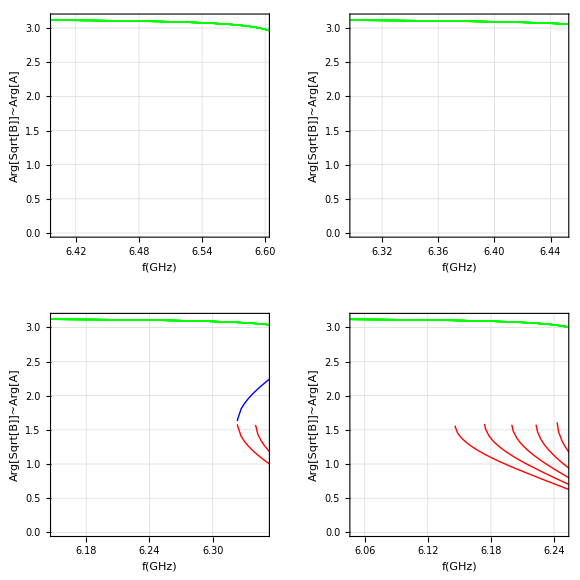

```mathematica
GraphicsGrid[{{plotBphase1,plotBphase2},{plotBphase3,plotBphase4}}]
```

```mathematica
plotCphase1=Show[Table[plotBphase[0.22,v,500]/.para1,{v,10^-8,10^-7,2*10^-8}],PlotRange->{{5.9,6.1},All},FrameLabel->{" f(GHz) ","Arg[Sqrt[B]]~Arg[A]"," {v,e-8,e-7,2e-6},Q=500, p=0.01", ""},Frame->True];
```

```mathematica
plotCphase2=Show[Table[plotBphase[0.25,v,500]/.para1,{v,10^-8,10^-7,2*10^-8}],PlotRange->{{5.8,6},All},FrameLabel->{" f(GHz) ","Arg[Sqrt[B]]~Arg[A]"," {v,10^-6,10^-5,10^-6},Q=500, p=0.01", ""},Frame->True];
```

```mathematica
plotCphase3=Show[Table[plotBphase[0.28,v,500]/.para1,{v,10^-8,10^-7,2*10^-8}],PlotRange->{{5.7,5.9},All},FrameLabel->{" f(GHz) ","Arg[Sqrt[B]]~Arg[A]"," {v,10^-6,10^-5,10^-6},Q=600, p=0.01", ""},Frame->True];
```

```mathematica
plotCphase4=Show[Table[plotBphase[0.31,v,500]/.para1,{v,10^-8,10^-7,2*10^-8}],PlotRange->{{5.6,5.8},All},FrameLabel->{" f(GHz) ","Arg[Sqrt[B]]~Arg[A]"," {v,10^-6,10^-5,10^-6},Q=1000, p=0.01", ""},Frame->True];
```

$Aborted

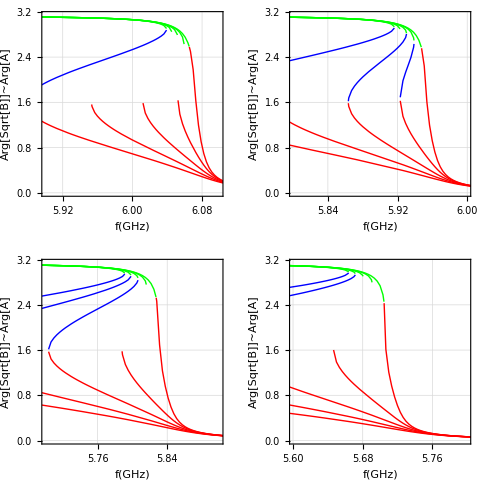

```mathematica
GraphicsGrid[{{plotCphase1,plotCphase2},{plotCphase3,plotCphase4}}]
```

## Theoretical Escape Rate

#### parameters near bifurcation B[Ω]

```mathematica
bmet[Ω_]:=1/27/Sqrt[βbplus[Ω]]*(Ω^2*(1+Sqrt[1-3/Ω^2])+9*Sqrt[1-3/Ω^2]-6+9/Ω^2)/;Ω>Ωc
bmetf[f_,fo_,p_,Q_]:=Block[{Ω=-2*Q(2Pi*f-ωeff[2*Pi*fo,p])/ωeff[2*Pi*fo,p]},1/27/Sqrt[βbplus[-Ω]]*(Ω^2*(1+Sqrt[1-3/Ω^2])+9*Sqrt[1-3/Ω^2]-6+9/Ω^2)/;f<fbc[fo,p,Q]]
```

```mathematica
pdyk[Ω_]:=2/3*(1-(1/Ω^2)^(1/2))/;Ω>Ωc
bdyk[Ω_]:=-pdyk[Ω]/Sqrt[βbplus[Ω]]*(5*pdyk[Ω]-3+3*(2pdyk[Ω]-1)^2(pdyk[Ω]-1)Ω^2)/;Ω>Ωc
```

```mathematica
bdykf[f_,fo_,p_,Q_]:=Block[{Ω=-2*Q(2Pi*f-ωeff[2*Pi*fo,p])/ωeff[2*Pi*fo,p]},bdyk[Ω]]
```

```mathematica
plotbΩ=Plot[{bmet[Ω*Ωc],bdyk[Ω*Ωc]},{Ω,1,10},Evaluate[MyOptions],FrameLabel->{"Ω/Ωc ","","b[Ω] Met & Dyk",""},Frame->True];
plotbf=Plot[{bmetf[f giga, 7 giga, 0.3, 500],bdykf[f giga, 7 giga, 0.3, 500]},{f,5.66,5.75},Evaluate[MyOptions],FrameLabel->{"f (Ghz) ","","b[f] Met & Dyk",""},Frame->True];
```

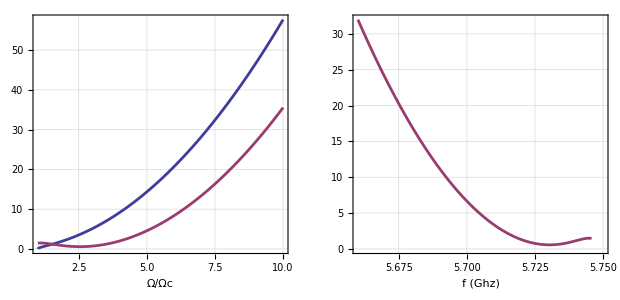

```mathematica
GraphicsRow[{plotbΩ,plotbf}]
```

#### Attempt Frequency ω_a

ωaredΩ=ωa/2/Pi
α=βd/βb=Vd^2/Vb^2

```mathematica
?feff
```

Global`feff

feff[f0_,p_,Q_]:=(f0 √(1-p))/(1+(√π)/(√π+π √(2 Q)))

```mathematica
ωaredΩ[Ω_,fo_,Q_,p_,α_]:=1/3/Sqrt[3]*2*Pi/Q*feff[fo,p]*Ω^2*Sqrt[Abs[1-α]]/;Ω>Ωc
```

```mathematica
ωared[f_,fo_,Q_,p_,β_]:=Block[{Ω=-2*Q*(f-feff[fo,p])/feff[fo,p]},feff[fo,p]/3/Sqrt[3]/Q*Ω^2*Sqrt[Abs[1-β/βbplusf[f,fo,p,Q]^2]]]/;( f<fbc[fo,p,Q]&&β<βbplusf[f,fo,p,Q]);
```

```mathematica
ωa[f_,fo_,Q_,p_,Vd_]:=Block[{Ω=-2*Q*(f-feff[fo,p])/feff[fo,p]},feff[fo,p]/3/Sqrt[3]/Q*Ω^2*Sqrt[Abs[1-Vd^2/Vdbplusf[f,fo,p,Q]^2]]]/;( f<fbc[fo,p,Q]&&Vd<Vdbplusf[f,fo,p,Q]);
```

```mathematica
plotωaredVsα[Ω_,fo_,Q_,p_,options__]:=Plot[nano ωaredΩ[Ω,fo,Q,p,α],{α,0,1},options,Evaluate[MyOptions],FrameLabel->{"α=βd/βb ","","ωa (GHz)",""},Frame->True,PlotRange->All]
plotωaredVsΩ[α_,fo_,Q_,p_,options__]:=Plot[nano ωaredΩ[Ω,fo,Q,p,α],{Ω,Ωc,7},options,Evaluate[MyOptions],FrameLabel->{"Ω ","","ωa (GHz)",""},Frame->True,PlotRange->All]
plottabωaredVsΩ=Show[Table[plotωaredVsΩ[α,7giga,500,.23,PlotStyle->{RGBColor[α,0,0],{{Thickness[0.008]}}}],{α ,0 ,1,.05}]];
plottabωaredVsα=Show[Table[plotωaredVsα[Ω,7giga,500,.23,PlotStyle->{RGBColor[Ω/7,0,0],{{Thickness[0.008]}}}],{Ω ,Ωc ,7,.25}]];
```

```mathematica
plotωaVsVd[f_,fo_,Q_,p_,options__]:=Plot[nano ωa[f,fo,Q,p,Vd micro],{Vd,0,Vdbplusf[f,fo,p,Q]/micro},options,Evaluate[MyOptions],FrameLabel->{"Vd (µV) ","","ωa (GHz)",""},Frame->True,PlotRange->All];
tableplotωaVsVd:=Show[Table[plotωaVsVd[f giga,7giga,500,.23,PlotStyle->{RGBColor[(f -5.93)/.096,0,0],{{Thickness[0.008]}}}],{f ,5.93 ,6.026,.005}]];
plotωaVsf[fo_,Q_,p_,Vd_,options__]:=Plot[nano ωa[f giga,fo,Q,p,Vd],{f,5.99,fbc[7,.23,500]},options,Evaluate[MyOptions],FrameLabel->{"f (GHz) ","","ωa (GHz)",""},Frame->True,PlotRange->{{5.99,6.027},All}];
tableplotωaVsf:=Show[Table[plotωaVsf[7giga,500,.23,Vd micro,  PlotStyle->{RGBColor[Vd/.14,0,0],{{Thickness[0.008]}}}],{Vd ,0,.14,.005}]];
```

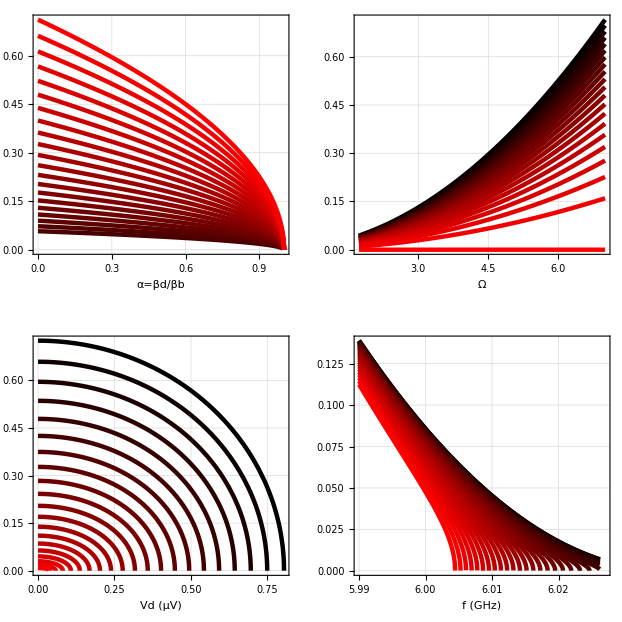

```mathematica
GraphicsGrid[{{plottabωaredVsα,plottabωaredVsΩ},{tableplotωaVsVd,tableplotωaVsf}}]
```

-> Erreur dans le quadrant bas/droit: ???

#### barrier height ΔU

formule de M. M.  page 92 ΔU adimensionné (en Unitée de Ej/p^2)

```mathematica
ΔUmetred[p_,Q_,Ω_/;Ω>Ωc,α_]:=8.*Sqrt[2]/3/p^2/Q*(βbplus[Ω])^(3)*Ω^2/Sqrt[bmet[Ω]]*(Abs[1-α])^(3/2);
ΔUmet[p_,Q_,Ω_/;Ω>Ωc,β_]:=8.*Sqrt[2]/3/p^2/Q*βbplus[Ω]^(3)*Ω^2/Sqrt[bmet[Ω]]*(Abs[1-β/βbplus[Ω]])^(3/2)/;β<βbplus[Ω];
ΔUmetfβ[p_,Q_,f_,fo_,β_]:=Block[{Ω=-2*Q*(f-feff[fo,p])/feff[fo,p]},ΔUmet[p,Q,Ω,β]]/;( f<fbc[fo,p,Q]&&β<βbplusf[f,fo,p,Q]);
ΔUmetfVd[p_,Q_,f_,fo_,Vd_]:=Block[{Ω=-2*Q*(f-feff[fo,p])/feff[fo,p]},ΔUmetred[p,Q,Ω,(Vd/Vdbplusf[f,fo,p,Q])^2]]/;( f<fbc[fo,p,Q]&&Vd<Vdbplusf[f,fo,p,Q]);
ΔUmoired[p_,Q_,Ω_/;Ω>Ωc,α_]:=32/9/Sqrt[3]*Ω/Q/p^2*(Abs[1-α])^(3/2);
ΔUmoifβ[p_,Q_,f_,fo_,β_]:=Block[{Ω=-2*Q*(f-feff[fo,p])/feff[fo,p]},ΔUmoired[p,Q,Ω,β/βbplus[Ω]]]/;β<βbplus[Ω];
ΔUmoifVd[p_,Q_,f_,fo_,Vd_]:=Block[{Ω=-2*Q*(f-feff[fo,p])/feff[fo,p]},ΔUmoired[p,Q,Ω,(Vd/Vdbplusf[f,fo,p,Q])^2]]/;β<βbplus[Ω];
```

```mathematica
plotΔUmetred[p_,Q_,Ω_,options__]:=Plot[ΔUmetred[p,Q,Ω,α],{α,0,1},options,Evaluate [MyOptions],FrameLabel->{"α=β/βbplus","ΔU/Ej","Barrier Height",""},PlotRange->All]
plotΔUmet[p_,Q_,Ω_,options__]:=Plot[ΔUmet[p,Q,Ω,β/βbplus[Ω]],{β,0,βbplus[Ω]},options,Evaluate [MyOptions],FrameLabel->{"β","ΔU/Ej","Barrier Height",""},PlotRange->All]
plotΔUmetredΩ[p_,Q_,α_,options__]:=Plot[ΔUmetred[p,Q,Ω,α],{Ω,1.1Ωc,7},options,Evaluate [MyOptions],FrameLabel->{"Ω","ΔU/Ej","Barrier Height",""},PlotRange->All]
```

```mathematica
plotΔUmoired[p_,Q_,Ω_,options__]:=Plot[ΔUmoired[p,Q,Ω,α],{α,0,1},options,Evaluate [MyOptions],FrameLabel->{"α=β/βbplus","ΔU/Ej","Barrier Height",""},PlotRange->All]
plotΔUmoi[p_,Q_,Ω_,options__]:=Plot[ΔUmoired[p,Q,Ω,β/βbplus[Ω]],{β,0,βbplus[Ω]},options,Evaluate [MyOptions],FrameLabel->{"β","ΔU/Ej","Barrier Height",""},PlotRange->All]
plotΔUmoiredΩ[p_,Q_,α_,options__]:=Plot[ΔUmoired[p,Q,Ω,α],{Ω,1.1Ωc,7},options,Evaluate [MyOptions],FrameLabel->{"Ω","ΔU/Ej","Barrier Height",""},PlotRange->All]
```

```mathematica
plotΔ[p_,Q_,Ω_,options__]:=Plot[ΔUmetred[p,Q,Ω,α],{α,0,1},options,Evaluate [MyOptions],FrameLabel->{"α=β/βbplus","ΔU/Ej","Barrier Height",""},PlotRange->All]
```

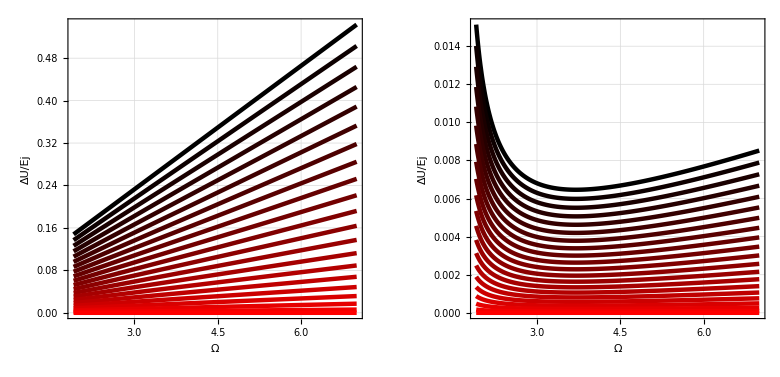

```mathematica
GraphicsRow[{Show[Table[plotΔUmoiredΩ[.23,500,α,PlotStyle->{RGBColor[α,0,0],{{Thickness[0.008]}}}],{α,0,1,.05}]],Show[Table[plotΔUmetredΩ[.23,500,α,PlotStyle->{RGBColor[α,0,0],{{Thickness[0.008]}}}],{α,0,1,.05}]]}]
```

```mathematica
plottableΔUred=Show[Table[plotΔUmetred[.23,500,Ω,PlotStyle->{RGBColor[Ω/10,0,0],{{Thickness[0.008]}}}],{Ω,1.1Ωc,10,.25}]];
plottableΔU=Show[Table[plotΔUmet[.23,500,Ω,PlotStyle->{RGBColor[Ω/10,0,0],{{Thickness[0.008]}}}],{Ω,1.1Ωc,10,.25}]];
```

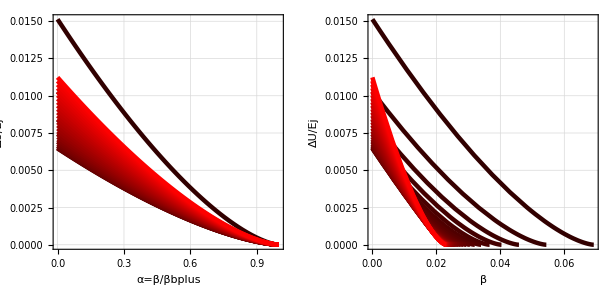

```mathematica
GraphicsRow[{plottableΔUred,plottableΔU}]
```

Ejj[zo_, ωo_, p_] énergie de la jonction josephson en Kelvin (de l'ordre de 7K)

```mathematica
ΔUmet2[p_,Q_,Ω_/;Ω>Ωc,β_,Tesc_,fo_]:=Ejj[50,2*Pi*fo,p]/Tesc*8.*Sqrt[2]/3/p^2/Q*βbplus[Ω]^(3)*Ω^2/bmet[Ω]*(Abs[1-β/βbplus[Ω]])^(3/2)/;β<βbplus[Ω];
```

```mathematica
plotΔUmet2[p_,Q_,Ω_,Tesc_,fo_,options__]:=Plot[ΔUmet2[p,Q,Ω,β,Tesc,fo],{β,0,βbplus[Ω]},options,Evaluate [MyOptions],FrameLabel->{"β","ΔU/kbTesc","Barrier Height",""},PlotRange->All]
```

```mathematica
plottableΔU1=Show[Table[plotΔUmet2[.1,200,Ω,.03,7 giga,PlotStyle->{RGBColor[Ω/10,0,0],{{Thickness[0.008]}}}],{Ω,1.01Ωc,10,.1}]];
```

```mathematica
plottableΔU=Show[Table[plotΔUmet2[.1,200,Ω,.03,7 giga,PlotStyle->{RGBColor[Ω/10,0,0],{{Thickness[0.008]}}}],{Ω,1.01Ωc,10,.1}]];
```

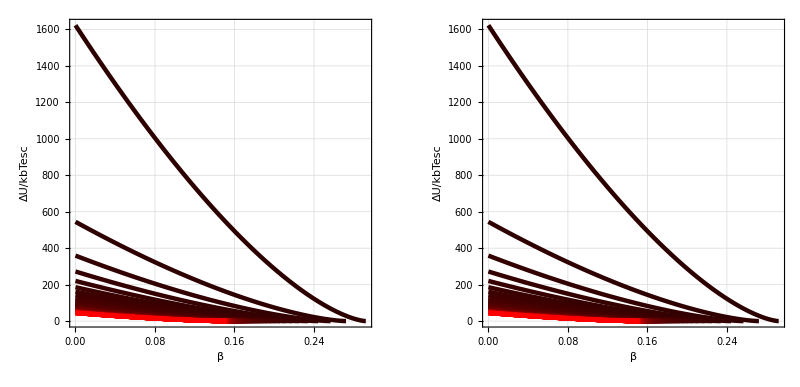

```mathematica
GraphicsRow[{plottableΔU1,plottableΔU}]
```

#### Escape rate γ

```mathematica
VdbplusΩ[Ω_/;Ω>Ωc,f_,p_,Q_]
```

```mathematica
Tesc=hbar*ω/2kb
```

```mathematica
Tesc[ωo_,p_,Q_]:=hbar*ωeff[ωo,p]/2/kb;
```

```mathematica
ΔUmoired[Q_,Ω_/;Ω>Ωc,α_]
```

ΔUmoired[Q_,Ω_/;Ω>Ωc,α_]

```mathematica
γmoi[fo_,p_,Q_,Ω_,α_]:=ωaredΩ[Ω,fo,Q,p,α]/2/Pi*Exp[-ΔUmoired[p,Q,Ω,α]*Ejj[50,2*Pi*fo,p]/Tesc[2*Pi*fo,p,Q]];
γmoi2[fo_,p_,Q_,Ω_,α_,Techap_]:=ωaredΩ[Ω,fo,Q,p,α]/2/Pi*Exp[-ΔUmoired[p,Q,Ω,α]*Ejj[50,2*Pi*fo,p]/Techap];
```

```mathematica
plotγmoi1[fo_,p_,Q_,Ω_,options__]:=Plot[nano γmoi[fo,p,Q,Ω,α],{α,0,1},options,Evaluate [MyOptions],FrameLabel->{"α","γ_esc (GHz)"," Escape Rate",""},PlotRange->All]
plotγmoi2[fo_,p_,Q_,α_,options__]:=Plot[nano γmoi[fo,p,Q,Ω,α],{Ω,1.1Ωc,7},options,Evaluate [MyOptions],FrameLabel->{"Ω","γ_esc (GHz)"," Escape Rate",""},PlotRange->All]
```

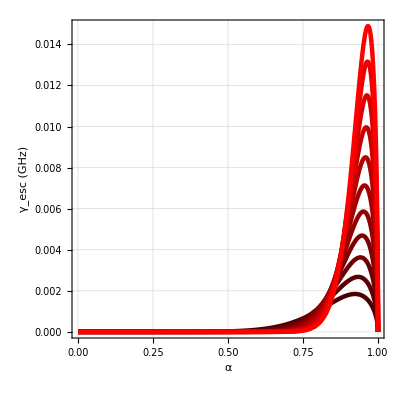

```mathematica
plottableγmoi=Show[Table[plotγmoi1[7giga,.23,500,Ω,PlotStyle->{RGBColor[Ω/7,0,0],{{Thickness[0.008]}}}],{Ω,2,7,.5}]]
```

```mathematica
γred[fo_,p_,Q_,Ω_,α_,Tesc_]:=ωaredΩ[Ω,fo,Q,p,α]/2/Pi*Exp[-ΔUmetred[p,Q,Ω,α]*Ejj[50,2*Pi*fo,p]/Tesc];
γred2[fo_,p_,Q_,Ω_,β_,Tesc_]:=γred[fo,p,Q,Ω,β/βbplus[Ω],Tesc]/;β<βbplus[Ω];
γred3[fo_,p_,Q_,Ω_,Vd_,Tesc_]:=γred[fo,p,Q,Ω,(Vd/VdbplusΩ[Ω,fo,p,Q])^2,Tesc]/;Vd<VdbplusΩ[Ω,fo,p,Q];
```

```mathematica
plotγred1[fo_,p_,Q_,Ω_,Tesc_,options__]:=Plot[nano γred[fo,p,Q,Ω,α,Tesc],{α,0,1},options,Evaluate [MyOptions],FrameLabel->{"α","γ_esc (GHz)"," Escape Rate",""},PlotRange->All]
plotγred2[fo_,p_,Q_,α_,Tesc_,options__]:=Plot[nano γred[fo,p,Q,Ω,α,Tesc],{Ω,1.1Ωc,7},options,Evaluate [MyOptions],FrameLabel->{"Ω","γ_esc (GHz)"," Escape Rate",""},PlotRange->All]
plotγred21[fo_,p_,Q_,Ω_,Tesc_,options__]:=Plot[nano γred2[fo,p,Q,Ω,β,Tesc],{β,.14,βbplus[Ω]},options,Evaluate [MyOptions],FrameLabel->{"β","γ_esc (GHz)"," Escape Rate",""},PlotRange->All]
plotγred22[fo_,p_,Q_,β_,Tesc_,options__]:=Plot[nano γred2[fo,p,Q,Ω,β,Tesc],{Ω,Ωc,7},options,Evaluate [MyOptions],FrameLabel->{"Ω","γ_esc (GHz)"," Escape Rate",""},PlotRange->All]
plotγred31[fo_,p_,Q_,Ω_,Tesc_,options__]:=Plot[nano γred3[fo,p,Q,Ω,Vd micro,Tesc],{Vd,0,VdbplusΩ[Ω,fo,p,Q]/micro},options,Evaluate [MyOptions],FrameLabel->{"Vd (µV)","γ_esc (GHz)"," Escape Rate",""},PlotRange->All]
plotγred32[fo_,p_,Q_,Vd_,Tesc_,options__]:=Plot[nano γred3[fo,p,Q,Ω,Vd,Tesc],{Ω,Ωc,4},options,Evaluate [MyOptions],FrameLabel->{"Ω","γ_esc (GHz)"," Escape Rate",""},PlotRange->All]
```

```mathematica
plot2tableγ3red170mK=Show[Table[plotγred32[7 giga,.1,200,Vd,.05,PlotStyle->{RGBColor[Vd/(1.2*10^-6),0,0],{{Thickness[0.008]}}}],{Vd,0,1.2*10^-6,10^-7}]];
plottableγ3red170mK=Show[Table[plotγred31[7giga,.18,200,Ω,.05,PlotStyle->{RGBColor[Ω/7,0,0],{{Thickness[0.008]}}}],{Ω,1.1Ωc,7,.5}]];
```

```mathematica
plottableγ2red170mK=Show[Table[plotγred21[7giga,.05,200,Ω,.05,PlotStyle->{RGBColor[Ω/7,0,0],{{Thickness[0.008]}}}],{Ω,1.1Ωc,7,.5}]];
plot2tableγ2red170mK=Show[Table[plotγred22[7giga,.05,200,β,.05,PlotStyle->{RGBColor[(β-.14)/.12,0,0],{{Thickness[0.008]}}}],{β,0.14,.26,.01}]];
```

```mathematica
plottableγred170mK=Show[Table[plotγred1[7giga,.18,400,Ω,.1,PlotStyle->{RGBColor[Ω/7,0,0],{{Thickness[0.008]}}}],{Ω,1.1Ωc,7,.5}]];
plottableγred300mK=Show[Table[plotγred1[7giga,.18,200,Ω,.1,PlotStyle->{RGBColor[Ω/7,0,0],{{Thickness[0.008]}}}],{Ω,1.1Ωc,7,.5}]];
plot2tableγred170mK=Show[Table[plotγred2[7giga,.18,400,α,.1,PlotStyle->{RGBColor[α,0,0],{{Thickness[0.008]}}}],{α,0,.95,.05}]];
plot2tableγred300mK=Show[Table[plotγred2[7giga,.18,200,α,.1,PlotStyle->{RGBColor[α,0,0],{{Thickness[0.008]}}}],{α,0,.95,.05}]];
```

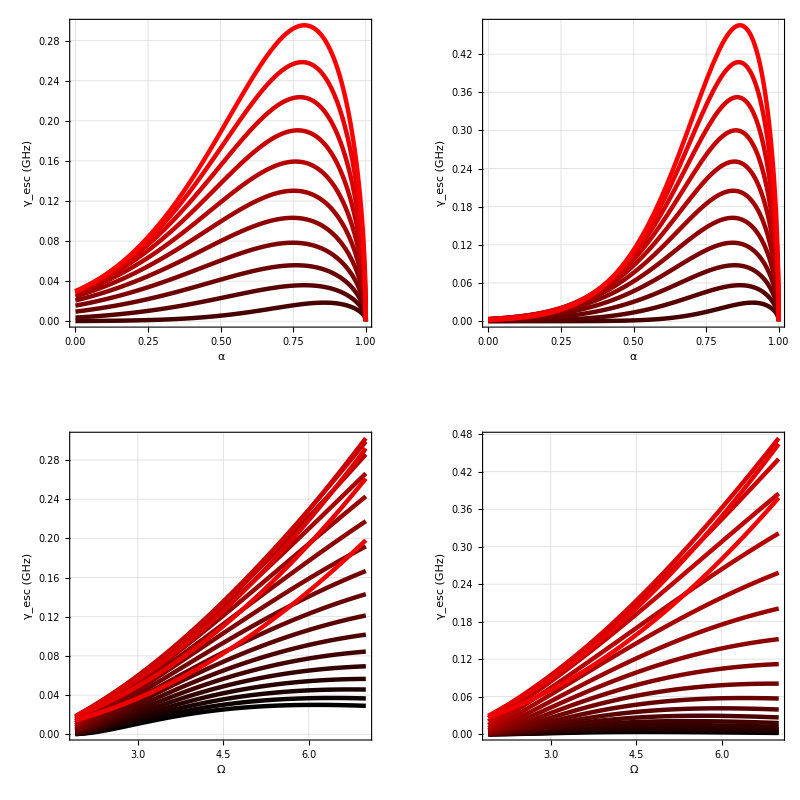

```mathematica
GraphicsGrid[{{plottableγred170mK,plottableγred300mK},{plot2tableγred170mK,plot2tableγred300mK}}]
```

```mathematica
plot2tableγ3red170mK=Show[Table[plotγred32[7 giga,.1,200,Vd micro,.05,PlotStyle->{RGBColor[Vd micro/(1.2*10^-6),0,0],{{Thickness[0.008]}}}],{Vd,0,1.2,.1}]];
plottableγ3red170mK=Show[Table[plotγred31[7giga,.18,200,Ω,.05,PlotStyle->{RGBColor[Ω/7,0,0],{{Thickness[0.008]}}}],{Ω,1.1Ωc,7,.5}]];
```

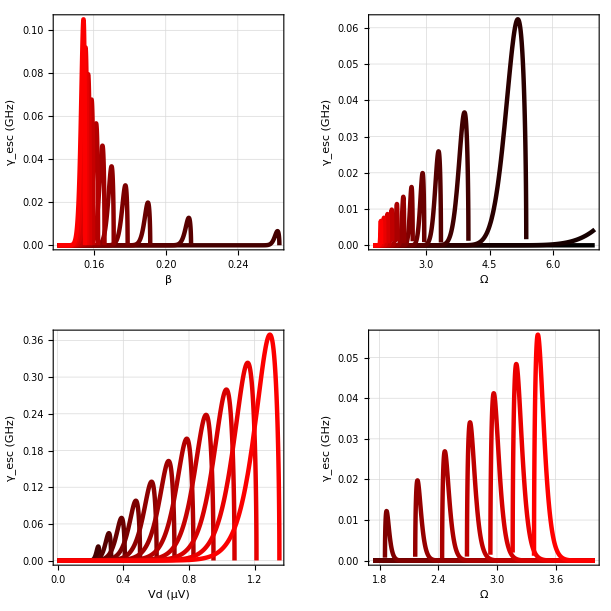

```mathematica
GraphicsGrid[{{plottableγ2red170mK,plot2tableγ2red170mK},{plottableγ3red170mK,plot2tableγ3red170mK}}]
```

#### Switching Proba

```mathematica
Pmoi[fo_,p_,Q_,Ω_,α_,τ_]:=1-Exp[-τ*nano*γmoi[fo,p,Q,Ω,α]];
Pmoi2[fo_,p_,Q_,Ω_,α_,τ_,Techap_]:=1-Exp[-τ*nano*γmoi2[fo,p,Q,Ω,α,Techap]]
```

```mathematica
plotPmoi[fo_,p_,Q_,Ω_,τ_,options__]:=Plot[Pmoi[fo,p,Q,Ω,α^2,τ],{α,0,1},options,Evaluate [MyOptions],FrameLabel->{"α","Pswitching","Switching Proba",""},PlotRange->All]
plotPmoi2[fo_,p_,Q_,Ω_,τ_,Techap_,options__]:=Plot[Pmoi2[fo,p,Q,Ω,α^2,τ,Techap],{α,0,1},options,Evaluate [MyOptions],FrameLabel->{"α","Pswitching","Switching Proba",""},PlotRange->All]
```

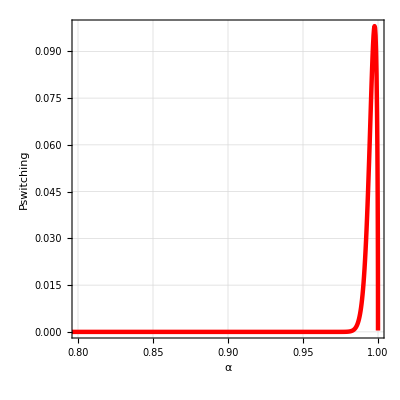

```mathematica
plotPmoi2[1.829 giga,.03,2286,6.9,300,.230,PlotStyle->{RGBColor[1,0,0],{{Thickness[0.008]}}},PlotRange->{{.8,1},All}]
```

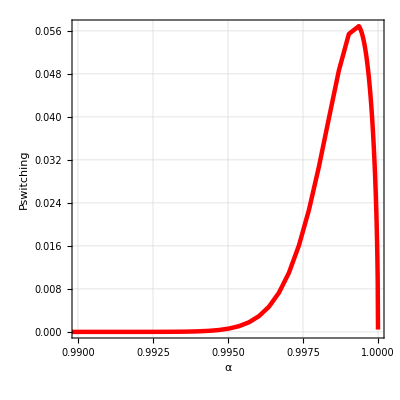

```mathematica
plotPmoi[1.829 giga,.03,2286,6.9,300,PlotStyle->{RGBColor[1,0,0],{{Thickness[0.008]}}},PlotRange->{{.99,1},All}]
```

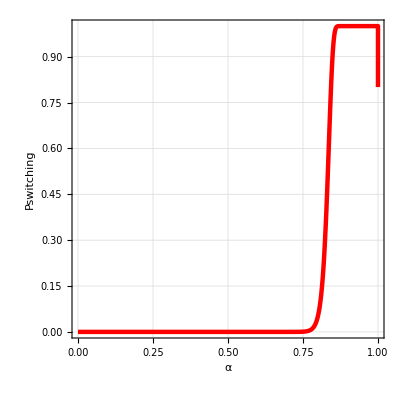

```mathematica
plotPmoi[1.7 giga,.13,1200,6.7,1000000,PlotStyle->{RGBColor[1,0,0],{{Thickness[0.008]}}},PlotRange->{{0,1},All}]
```

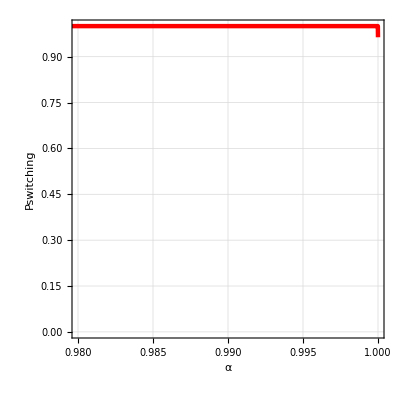

```mathematica
plotPmoi[9.9 giga,.05,936,3.44,1000000,PlotStyle->{RGBColor[1,0,0],{{Thickness[0.008]}}},PlotRange->{{.98,1},All}]
```

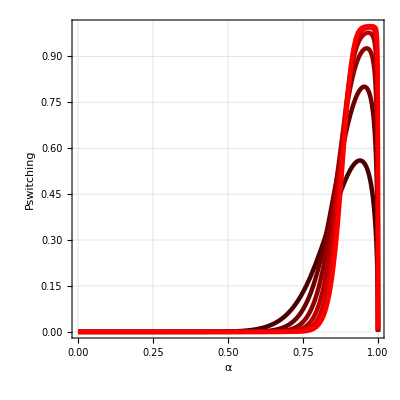

```mathematica
Show[Table[plotPmoi[7giga,.22,400,Ω,400,PlotStyle->{RGBColor[Ω/7,0,0],{{Thickness[0.008]}}}],{Ω,2,7,1}],PlotRange->{{0,1},All}]
```

```mathematica
γmoi[fo_,p_,Q_,Ω_,α_]
```

(ⅇ^(-(26.0022 √(1-p_) (1+(√π)/(√π+√2 π √Q_)) ΔUmoired[p_,Q_,Ω_,α_])/p_) ωaredΩ[Ω_,fo_,Q_,p_,α_])/(2 π)

```mathematica
Pred[fo_,p_,Q_,Ω_,α_,Tesc_,τ_]:=1-Exp[-τ*nano*γred[fo,p,Q,Ω,α,Tesc]]
Pred2[fo_,p_,Q_,Ω_,β_,Tesc_,τ_]:=1-Exp[-τ*nano*γred2[fo,p,Q,Ω,β,Tesc]]/;β<βbplus[Ω];
Pred3[fo_,p_,Q_,Ω_,Vd_,Tesc_,τ_]:=1-Exp[-τ*nano*γred3[fo,p,Q,Ω,Vd,Tesc]]/;Vd<VdbplusΩ[Ω,fo,p,Q];
```

```mathematica
VdbplusΩ[7,7 giga,.15,200]
```

1.81095×10^-6

```mathematica
plotPred[fo_,p_,Q_,Ω_,Tesc_,τ_,options__]:=Plot[Pred[fo,p,Q,Ω,α^2,Tesc,τ],{α,0,1},options,Evaluate [MyOptions],FrameLabel->{"α","Pswitching","Switching Proba",""},PlotRange->All]
plotPred2[fo_,p_,Q_,Ω_,Tesc_,τ_,options__]:=Plot[Pred2[fo,p,Q,Ω,β,Tesc,τ],{β,0,.12},options,Evaluate [MyOptions],FrameLabel->{"β","Pswitching","Switching Proba",""},PlotRange->All]
plotPred3[fo_,p_,Q_,Ω_,Tesc_,τ_,options__]:=Plot[Pred3[fo,p,Q,Ω,Vd,Tesc,τ],{Vd,0,5*10^-6},options,Evaluate [MyOptions],FrameLabel->{"Vd","Pswitching","Switching Proba",""},PlotRange->All]
```

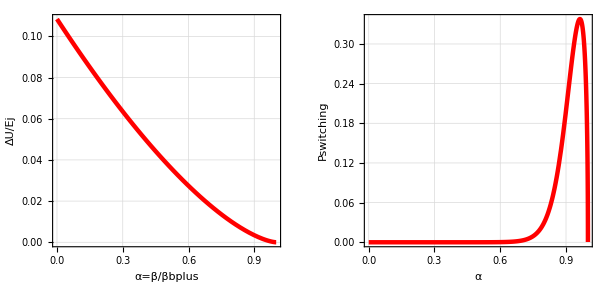

```mathematica
GraphicsRow[{plotΔUmetred[.03,2286,6.9,PlotStyle->{RGBColor[1,0,0],{{Thickness[0.008]}}}],plotPred[1.829giga,.03,2286,6.9,.23,300,PlotStyle->{RGBColor[1,0,0],{{Thickness[0.008]}}}]}]
```

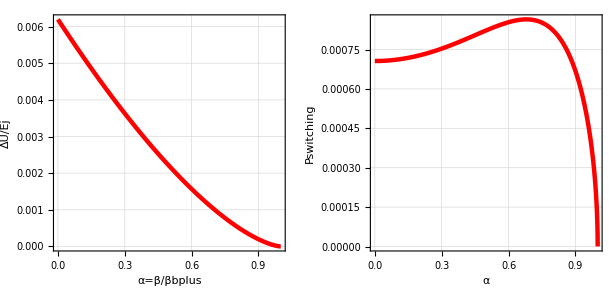

```mathematica
GraphicsRow[{plotΔUmoired[2286,6.9,PlotStyle->{RGBColor[1,0,0],{{Thickness[0.008]}}}],plotPmoi2[1.829giga,.03,2286,6.9,.23,300,PlotStyle->{RGBColor[1,0,0],{{Thickness[0.008]}}}]}]
```

```mathematica
Plot[1.829giga,.03,2286,6.9,.23,300,PlotStyle->{RGBColor[1,0,0],{{Thickness[0.008]}}}]
```

```mathematica
plottablePred1K=Show[Table[plotPred2[7giga,.15,200,Ω,.1,300,PlotStyle->{RGBColor[Ω/20,0,0],{{Thickness[0.008]}}}],{Ω,1.0001Ωc,20,1}]];
```

```mathematica
plot2tablePred1K=Show[Table[plotPred[7giga,.15,200,Ω,.1,300,PlotStyle->{RGBColor[Ω/20,0,0],{{Thickness[0.008]}}}],{Ω,Ωc,20,1}]];
```

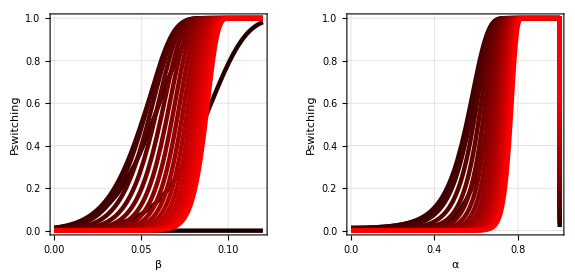

```mathematica
GraphicsRow[{plottablePred1K,plot2tablePred1K}]
```

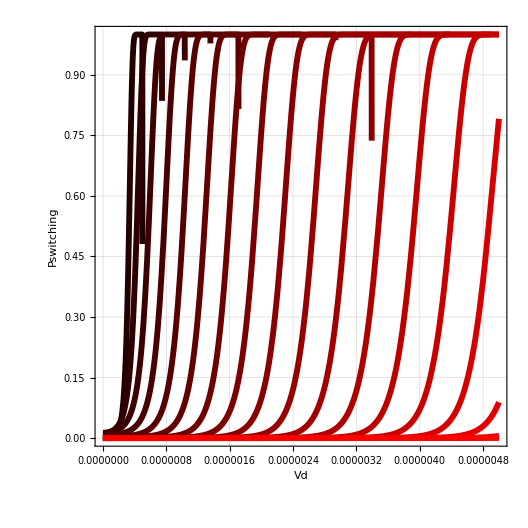

```mathematica
plot3tablePred1K=Show[Table[plotPred3[7giga,.15,200,Ω,.1,300,PlotStyle->{RGBColor[Ω/20,0,0],{{Thickness[0.008]}}}],{Ω,Ωc,20,1}]]
```

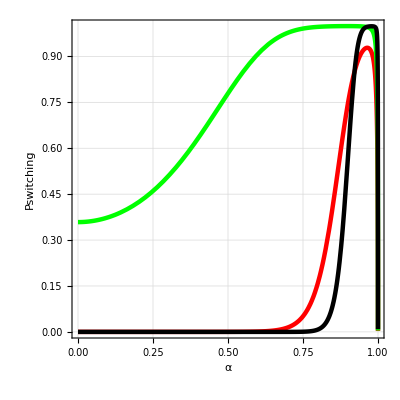

```mathematica
Show[{plotPred[1.829giga,.03,2226,6.9,.23,300,PlotStyle->{RGBColor[1,0,0],{{Thickness[0.008]}}}],plotPred[1.724giga,.13,1200,6.77,.02,300,PlotStyle->{RGBColor[0,1,0],{{Thickness[0.008]}}}],plotPred[9.928giga,.05,936,3.44,.23,300,PlotStyle->{RGBColor[0,0,0],{{Thickness[0.008]}}}]}]
```

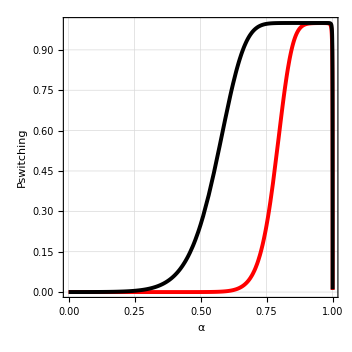

```mathematica
Show[{plotPred[11giga,.15,100,1.01Ωc,.2,3000,PlotStyle->{RGBColor[1,0,0],{{Thickness[0.008]}}}],plotPred[11giga,.15,100,1.15Ωc,.2,3000,PlotStyle->{RGBColor[0,0,0],{{Thickness[0.008]}}}]}]
```

#### S curve width

```mathematica
ΔUmetredInv[p_,Q_,α_,δUred_]:=Check[FindRoot[ΔUmetred[p,Q,Ω*Ωc,α]==δUred,{Ω,1.01,1.02}][[1,2]],"Not found"]
ΔUmetredInv2[p_,Q_,Ω_,δUred_]:=Check[FindRoot[ΔUmetred[p,Q,Ω,α]==δUred,{α,.5}][[1,2]],"Not found"]
```

```mathematica
ΔUmetredInv2[.2,500,1.1 Ωc,.05/Ejj[50,2*Pi*7 giga,.2]]
```

0.651095

```mathematica
plot1=ListPlot[Table[{Ω,ΔUmetredInv2[.2,500,Ω Ωc,.05/Ejj[50,2*Pi*7 giga,.2]]},{Ω,1.1,10,.01}],Evaluate[MyOptions],Joined->True,
FrameLabel->{"Ω/Ωc","α@U=kBTesc","s curve width vs detuning,Tesc=50mK",""},PlotRange->{All,{0,1}}];
plot2=ListPlot[Table[{Ω,ΔUmetredInv2[.2,500,Ω Ωc,.03/Ejj[50,2*Pi*7 giga,.2]]},{Ω,1.1,10,.01}],Evaluate[MyOptions],Joined->True,FrameLabel->{"Ω/Ωc","α@U=kBTesc","s curve width vs detuning,Tesc=30mK",""},PlotRange->{All,{0,1}}];
```

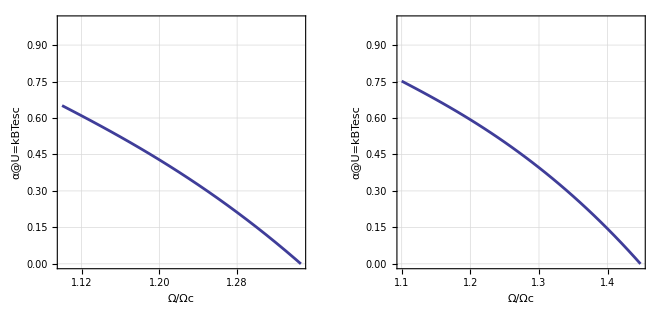

```mathematica
GraphicsRow[{plot1,plot2}]
```

```mathematica
zeαplot[p_,Q_,Tesc_]:=ListPlot[Table[{Ω,ΔUmetredInv2[p,Q,Ω Ωc,Tesc/Ejj[50,2*Pi*7 giga,p]]},{Ω,1.1,10,.01}],Evaluate[MyOptions],Joined->True,
FrameLabel->{"Ω/Ωc","α@U=kBTesc","s curve width vs detuning",""},PlotRange->{All,{0,1}}];
```

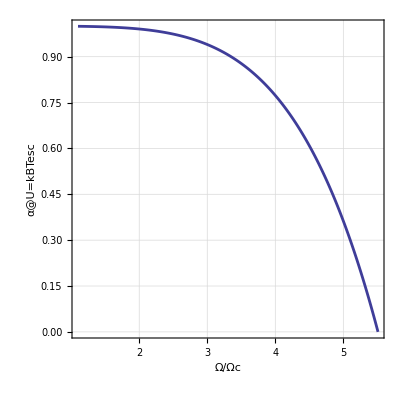

```mathematica
zeαplot[.01,500,.03]
```

δV/Vb avec δV=Vb-Vd (U=kbTesc)
->1-Sqrt[α(@U=kbTesc)

```mathematica
zeαplot2[p_,Q_,Tesc_]:=ListPlot[Table[{Ω,(1-Sqrt[ΔUmetredInv2[p,Q,Ω Ωc,Tesc/Ejj[50,2*Pi*7 giga,p]]])^(2/3)},{Ω,1.001,10,.002}],Evaluate[MyOptions],Joined->True,
FrameLabel->{"Ω/Ωc","(δV/Vb)^(2/3)@U=kbTesc","Scurve^2/3 & Tesc  vs detuning","kBTesc/Uo"},PlotRange->{All,{0,1}}];
```

```mathematica
plottest[p_,Q_,Tesc_]:=Plot[Tesc/(ΔUmetred[p,Q,Ω*Ωc,0]*Ejj[50,2*Pi*7 giga,p]),{Ω,1,10},PlotStyle->{RGBColor[1,0,0]},Evaluate[MyOptions]];
```

```mathematica
zebigplot[p_,Q_,Tesc1_,Tesc2_,Ωmax1_,Ωmax2_]:=GraphicsRow[{Show[{zeαplot2[p,Q,Tesc1],plottest[p,Q,Tesc1]},PlotRange->{{1,Ωmax1},{0,5}}],Show[{zeαplot2[p,Q,Tesc2],plottest[p,Q,Tesc2]},PlotRange->{{1,Ωmax2},{0,5}}]}]
```

Tesc via quantum activation Tesc=hbar*ω/2kb~150mK!!!!!!

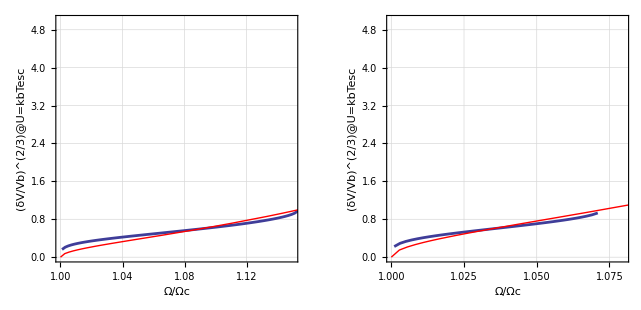

```mathematica
zebigplot[.22,400,h*feff[7 giga,.22]/2/kb,h*feff[7 giga,.22]/kb,1.15,1.08]
```

```mathematica
6./Sqrt[3]
```

3.4641

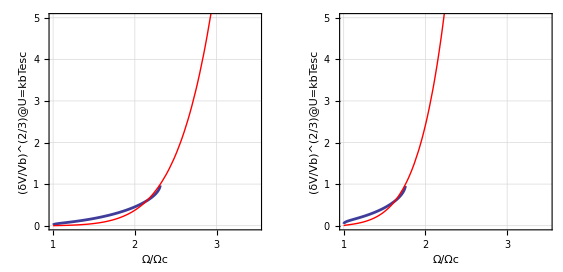

```mathematica
zebigplot[.04,400,h*feff[10 giga,.04]/2/kb,1.5,3.5,3.5]
```